# Velocity Dispersion and Power Spectra

## Circular Test Ring

#### Version 1 NFW parameters = {417.0 * pow(10,3) * mau * secyr, 36.54 * kpcau, 90.0 * pi / 180, 1.0, 1.0, 1.0} (NO TRIAXIALITY) 1000 test particles r0 = 15 kpc 100 timesteps of 1 Myr each dimensionless units, leapfrog

```mathematica
ch1pos = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",1;;1000,6;;7}];
ch1pos2 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",1000;;2000,6;;7}];
ch1pos3 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",2000;;3000,6;;7}];
ch1pos4 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",3000;;4000,6;;7}];
ch1pos5 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",4000;;5000,6;;7}];
ch1pos6 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",5000;;6000,6;;7}];
ch1pos7 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",6000;;7000,6;;7}];
ch1pos8 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",7000;;8000,6;;7}];
ch1pos9 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",8000;;9000,6;;7}];
ch1pos10 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",9000;;10000,6;;7}];
ch1pos11 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",10000;;11000,6;;7}];
ch1pos12 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",11000;;12000,6;;7}];
ch1pos13 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",12000;;13000,6;;7}];
ch1pos14 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",13000;;14000,6;;7}];
ch1pos15 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",14000;;15000,6;;7}];
ch1pos16 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",15000;;16000,6;;7}];
ch1pos17 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",16000;;17000,6;;7}];
ch1pos18 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",17000;;18000,6;;7}];
ch1pos19 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",18000;;19000,6;;7}];
ch1pos20 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",19000;;20000,6;;7}];
ch1pos21 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",20000;;21000,6;;7}];
ch1pos22 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",21000;;22000,6;;7}];
ch1pos23 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",22000;;23000,6;;7}];
ch1pos24 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",23000;;24000,6;;7}];
ch1pos25 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",24000;;25000,6;;7}];
ch1pos26 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",25000;;26000,6;;7}];
ch1pos27 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",26000;;27000,6;;7}];
ch1pos28 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",27000;;28000,6;;7}];
ch1pos29 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",28000;;29000,6;;7}];
ch1pos30 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",29000;;30000,6;;7}];
ch1pos31 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",30000;;31000,6;;7}];
ch1pos32 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",31000;;32000,6;;7}];
ch1pos33 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",32000;;33000,6;;7}];
ch1pos34 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",33000;;34000,6;;7}];
ch1pos35 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",34000;;35000,6;;7}];
ch1pos36 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",35000;;36000,6;;7}];
ch1pos100 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",99000;;100000,6;;7}];

ch1vel = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",1;;1000,4;;5}];
ch1vel2 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",1000;;2000,4;;5}];
ch1vel3 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",2000;;3000,4;;5}];
ch1vel4 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",3000;;4000,4;;5}];
ch1vel5 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",4000;;5000,4;;5}];
ch1vel6 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",5000;;6000,4;;5}];
ch1vel7 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",6000;;7000,4;;5}];
ch1vel8 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",7000;;8000,4;;5}];
ch1vel9 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",8000;;9000,4;;5}];
ch1vel10 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",9000;;10000,4;;5}];
ch1vel11 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",10000;;11000,4;;5}];
ch1vel12 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",11000;;12000,4;;5}];
ch1vel13 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",12000;;13000,4;;5}];
ch1vel14 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",13000;;14000,4;;5}];
ch1vel15 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",14000;;15000,4;;5}];
ch1vel16 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",15000;;16000,4;;5}];
ch1vel17 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",16000;;17000,4;;5}];
ch1vel18 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",17000;;18000,4;;5}];
ch1vel19 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",18000;;19000,4;;5}];
ch1vel20 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",19000;;20000,4;;5}];
ch1vel21 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",20000;;21000,4;;5}];
ch1vel22 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",21000;;22000,4;;5}];
ch1vel23 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",22000;;23000,4;;5}];
ch1vel24 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",23000;;24000,4;;5}];
ch1vel25 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",24000;;25000,4;;5}];
ch1vel26 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",25000;;26000,4;;5}];
ch1vel27 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",26000;;27000,4;;5}];
ch1vel28 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",27000;;28000,4;;5}];
ch1vel29 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",28000;;29000,4;;5}];
ch1vel30 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",29000;;30000,4;;5}];
ch1vel31 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",30000;;31000,4;;5}];
ch1vel32 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",31000;;32000,4;;5}];
ch1vel33 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",32000;;33000,4;;5}];
ch1vel34 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",33000;;34000,4;;5}];
ch1vel35 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test1.csv",{"Data",34000;;35000,4;;5}];


ch1AM1 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM1.csv",{"Data",1,1;;1000}];
ch1AM2 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM1.csv",{"Data",2,1;;1000}];
ch1AM3 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM1.csv",{"Data",3,1;;1000}];
ch1AM4 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM1.csv",{"Data",4,1;;1000}];
ch1AM5 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM1.csv",{"Data",5,1;;1000}];
ch1AM6 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM1.csv",{"Data",6,1;;1000}];
ch1AM7 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM1.csv",{"Data",7,1;;1000}];
ch1AM8 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM1.csv",{"Data",8,1;;1000}];
ch1AM9 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM1.csv",{"Data",9,1;;1000}];
ch1AM10 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM1.csv",{"Data",10,1;;1000}];
ch1AM11 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM1.csv",{"Data",11,1;;1000}];
ch1AM12 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM1.csv",{"Data",12,1;;1000}];
ch1AM13 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM1.csv",{"Data",13,1;;1000}];
ch1AM14 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM1.csv",{"Data",14,1;;1000}];
ch1AM15 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM1.csv",{"Data",15,1;;1000}];
ch1AM16 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM1.csv",{"Data",16,1;;1000}];
ch1AM17 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM1.csv",{"Data",17,1;;1000}];
ch1AM18 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM1.csv",{"Data",18,1;;1000}];
ch1AM19 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM1.csv",{"Data",19,1;;1000}];
ch1AM20 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM1.csv",{"Data",20,1;;1000}];
ch1AM21 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM1.csv",{"Data",21,1;;1000}];
ch1AM22 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM1.csv",{"Data",22,1;;1000}];
ch1AM23 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM1.csv",{"Data",23,1;;1000}];
ch1AM24 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM1.csv",{"Data",24,1;;1000}];
ch1AM25 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM1.csv",{"Data",25,1;;1000}];
ch1AM26 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM1.csv",{"Data",26,1;;1000}];
ch1AM27 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM1.csv",{"Data",27,1;;1000}];
ch1AM28 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM1.csv",{"Data",28,1;;1000}];
ch1AM29 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM1.csv",{"Data",29,1;;1000}];
ch1AM30 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM1.csv",{"Data",30,1;;1000}];
ch1AM31 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM1.csv",{"Data",31,1;;1000}];
ch1AM32 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM1.csv",{"Data",32,1;;1000}];
ch1AM33 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM1.csv",{"Data",33,1;;1000}];
ch1AM34 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM1.csv",{"Data",34,1;;1000}];
ch1AM35 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM1.csv",{"Data",35,1;;1000}];
ch1AM36 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM1.csv",{"Data",36,1;;1000}];
ch1AM100 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM1.csv",{"Data",100,1;;1000}];
ch1AM =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM1.csv",{"Data",1;;100,1}]


ch1SD = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/SD1.csv",{"Data",1;;101,1;;2}];
```

{6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319,6.28319}

#### Position:

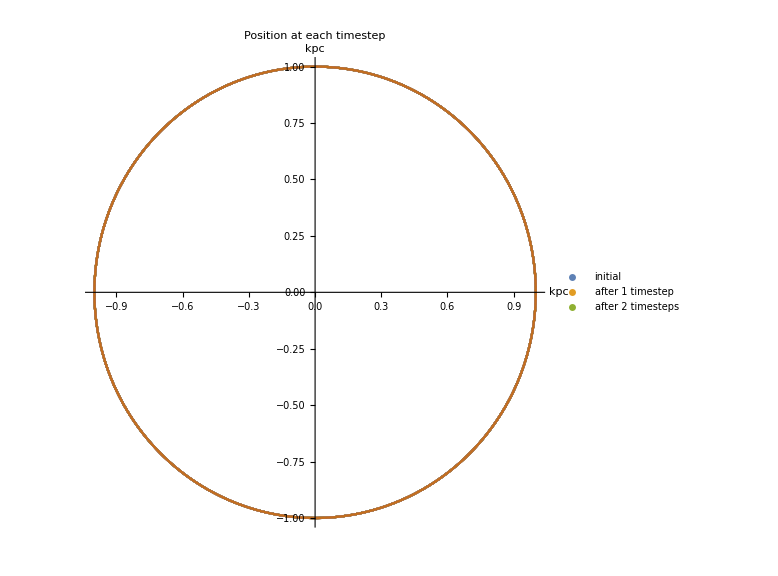

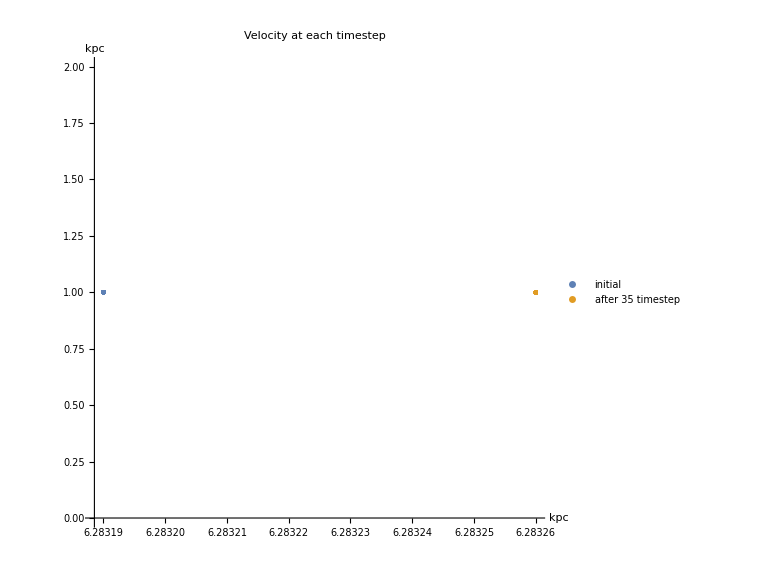

```mathematica
ch1posgraph = ListPlot[{ch1pos,ch1pos2,ch1pos3,ch1pos4,ch1pos5,ch1pos6,ch1pos7,ch1pos8,ch1pos9,ch1pos10,ch1pos11,ch1pos12,ch1pos13,ch1pos14,ch1pos15,ch1pos16,ch1pos17,ch1pos18,ch1pos19,ch1pos20,ch1pos21,ch1pos22,ch1pos23,ch1pos24,ch1pos25,ch1pos26,ch1pos27,ch1pos28,ch1pos29,ch1pos30,ch1pos31,ch1pos32,ch1pos33,ch1pos34,ch1pos35,ch1pos100},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"initial","after 1 timestep","after 2 timesteps"},AxesLabel->{"kpc","kpc"}, PlotLabel->"Position at each timestep"]
ch1velgraph = ListPlot[{ch1vel,ch1vel35},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"initial","after 35 timestep","after 2 timesteps"},AxesLabel->{"kpc","kpc"}, PlotLabel-> "Velocity at each timestep"]
```

#### Velocity Dispersion

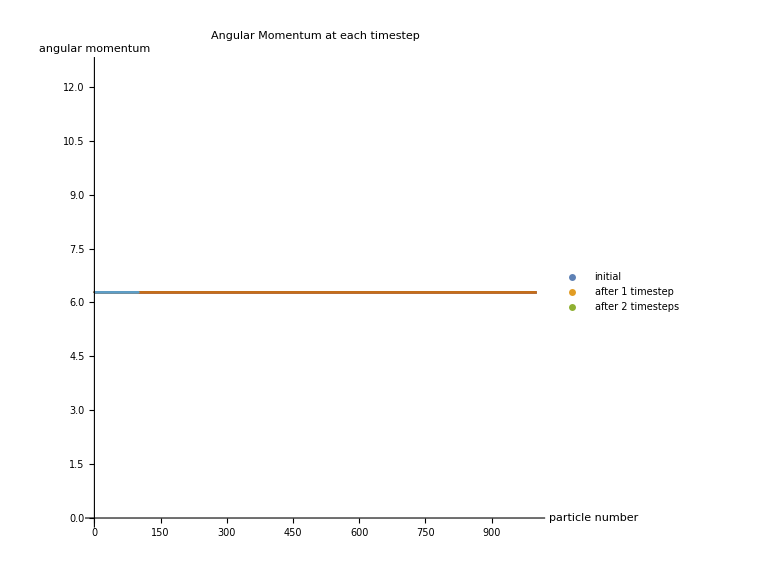

```mathematica
ch1AMgraph = ListPlot[{ch1AM1,ch1AM2,ch1AM3,ch1AM4,ch1AM5,ch1AM6,ch1AM7,ch1AM8,ch1AM9,ch1AM10,ch1AM11,ch1AM12,ch1AM13,ch1AM14,ch1AM15,ch1AM16,ch1AM17,ch1AM18,ch1AM19,ch1AM20,ch1AM100,ch1AM},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"initial","after 1 timestep","after 2 timesteps"},AxesLabel->{"particle number","angular momentum"}, PlotLabel-> "Angular Momentum at each timestep"]
```

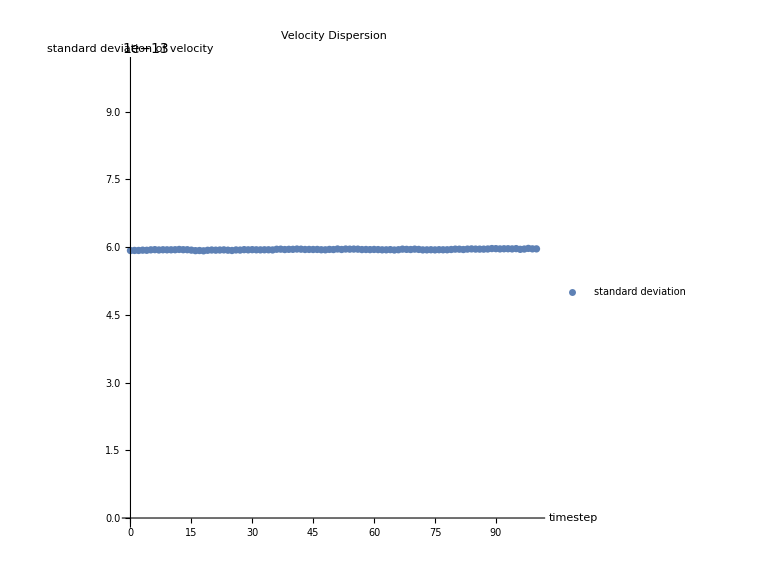

```mathematica
ch1SDgraph = ListPlot[{ch1SD},PlotRange->{{0,100},{0,0.000000000001}},AspectRatio->1,ImageSize->Large,PlotLegends->{"standard deviation"},AxesLabel->{"timestep","standard deviation of velocity"}, PlotLabel-> "Velocity Dispersion"]
```

```mathematica
)
```

#### Version 2: fewer particles, more timesteps NFW parameters = {417.0 * pow(10,3) * mau * secyr, 36.54 * kpcau, 90.0 * pi / 180, 1.0, 1.0, 1.0} (NO TRIAXIALITY) 10 test particles r0 = 15 kpc 1000 timesteps of 100, 000 years each dimensionless units, leapfrogs

```mathematica
ch2pos1 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",1;;10,6;;7}];
ch2pos2 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",10;;20,6;;7}];
ch2pos3 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",20;;30,6;;7}];
ch2pos4 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",30;;40,6;;7}];
ch2pos5 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",40;;50,6;;7}];
ch2pos6 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",50;;60,6;;7}];
ch2pos7 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",60;;70,6;;7}];
ch2pos8 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",70;;80,6;;7}];
ch2pos9 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",80;;90,6;;7}];
ch2pos10 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",90;;100,6;;7}];
ch2pos11 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",100;;110,6;;7}];
ch2pos12 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",110;;120,6;;7}];
ch2pos13 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",120;;130,6;;7}];
ch2pos14 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",130;;140,6;;7}];
ch2pos15 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",140;;150,6;;7}];
ch2pos16 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",150;;160,6;;7}];
ch2pos17 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",160;;170,6;;7}];
ch2pos18 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",170;;180,6;;7}];
ch2pos19 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",180;;190,6;;7}];
ch2pos20 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",190;;200,6;;7}];
ch2pos21 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",200;;210,6;;7}];
ch2pos22 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",210;;220,6;;7}];
ch2pos23 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",220;;230,6;;7}];
ch2pos24 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",230;;240,6;;7}];
ch2pos25 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",240;;250,6;;7}];
ch2pos26 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",250;;260,6;;7}];
ch2pos27 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",260;;270,6;;7}];
ch2pos28 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",270;;280,6;;7}];
ch2pos29 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",280;;290,6;;7}];
ch2pos30 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",290;;300,6;;7}];
ch2pos31 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",300;;310,6;;7}];
ch2pos32 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",310;;320,6;;7}];
ch2pos33 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",320;;330,6;;7}];
ch2pos34 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",330;;340,6;;7}];
ch2pos35 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",340;;350,6;;7}];
ch2pos36 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",350;;360,6;;7}];
ch2pos100 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",990;;1000,6;;7}];
ch2pos200 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",1990;;2000,6;;7}];
ch2pos300 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",2990;;3000,6;;7}];
ch2pos400 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",3990;;4000,6;;7}];
ch2pos500 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",4990;;5000,6;;7}];
ch2pos600 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",5990;;6000,6;;7}];
ch2pos700 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",6990;;7000,6;;7}];
ch2pos800 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",7990;;8000,6;;7}];
ch2pos900 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",8990;;9000,6;;7}];
ch2pos1000 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",9990;;10000,6;;7}];

ch2vel = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",1;;10,4;;5}];
ch2vel2 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",10;;20,4;;5}];
ch2vel3 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",20;;30,4;;5}];
ch2vel4 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",30;;40,4;;5}];
ch2vel5 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",40;;50,4;;5}];
ch2vel6 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",50;;60,4;;5}];
ch2vel7 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",60;;70,4;;5}];
ch2vel8 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",70;;80,4;;5}];
ch2vel9 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",80;;90,4;;5}];
ch2vel10 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",90;;100,4;;5}];
ch2vel11 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",100;;110,4;;5}];
ch2vel12 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",110;;120,4;;5}];
ch2vel13 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",120;;130,4;;5}];
ch2vel14 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",130;;140,4;;5}];
ch2vel15 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",140;;150,4;;5}];
ch2vel16 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",150;;160,4;;5}];
ch2vel17 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",160;;170,4;;5}];
ch2vel18 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",170;;180,4;;5}];
ch2vel19 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",180;;190,4;;5}];
ch2vel20 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",190;;200,4;;5}];
ch2vel21 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",200;;210,4;;5}];
ch2vel22 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",210;;220,4;;5}];
ch2vel23 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",220;;230,4;;5}];
ch2vel24 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",230;;240,4;;5}];
ch2vel25 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",240;;250,4;;5}];
ch2vel26 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",250;;260,4;;5}];
ch2vel27 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",260;;270,4;;5}];
ch2vel28 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",270;;280,4;;5}];
ch2vel29 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",280;;290,4;;5}];
ch2vel30 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",290;;300,4;;5}];
ch2vel31 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",300;;310,4;;5}];
ch2vel32 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",310;;320,4;;5}];
(*ch2vel33 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",32000;;33000,4;;5}];
ch2vel34 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",33000;;34000,4;;5}];
ch2vel35 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",34000;;35000,4;;5}];
ch2vel36 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test2.csv",{"Data",35000;;36000,4;;5}];

ch2velgraph = ListPlot[{ch2vel,ch2vel29},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"initial","after 35 timestep","after 2 timesteps"},AxesLabel->{"kpc","kpc"}, PlotLabel-> "Velocity at each timestep"]
*)
ch2AM1 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",1,1;;10}];
ch2AM2 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",2,1;;10}];
ch2AM3 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",3,1;;10}];
ch2AM4 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",4,1;;10}];
ch2AM5 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",5,1;;10}];
ch2AM6 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",6,1;;10}];
ch2AM7 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",7,1;;10}];
ch2AM8 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",8,1;;10}];
ch2AM9 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",9,1;;10}];
ch2AM10 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",10,1;;10}];
ch2AM11 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",11,1;;10}];
ch2AM12 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",12,1;;10}];
ch2AM13 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",13,1;;10}];
ch2AM14 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",14,1;;10}];
ch2AM15 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",15,1;;10}];
ch2AM16 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",16,1;;10}];
ch2AM17 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",17,1;;10}];
ch2AM18 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",18,1;;10}];
ch2AM19 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",19,1;;10}];
ch2AM20 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",20,1;;10}];
ch2AM21 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",21,1;;10}];
ch2AM22 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",22,1;;10}];
ch2AM23 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",23,1;;10}];
ch2AM24 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",24,1;;10}];
ch2AM25 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",25,1;;10}];
ch2AM26 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",26,1;;10}];
ch2AM27 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",27,1;;10}];
ch2AM28 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",28,1;;10}];
ch2AM29 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",29,1;;10}];
ch2AM30 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",30,1;;10}];
ch2AM31 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",31,1;;10}];
ch2AM32 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",32,1;;10}];
ch2AM33 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",33,1;;10}];
ch2AM34 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",34,1;;10}];
ch2AM35 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",35,1;;10}];
ch2AM36 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",36,1;;10}]; 
ch2AM100 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",100,1;;10}];
ch2AM200 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",200,1;;10}];
ch2AM300 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",300,1;;10}];
ch2AM400 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",400,1;;10}];
ch2AM500 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",500,1;;10}];
ch2AM600 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",600,1;;10}];
ch2AM700 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",700,1;;10}];
ch2AM800 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",800,1;;10}];
ch2AM900 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",900,1;;10}];
ch2AM1000 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",1000,1;;10}];
ch2AM = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",1;;1000,1}];


ch2SD = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/SD2.csv",{"Data",1;;1000,1;;2}];
```

#### Position

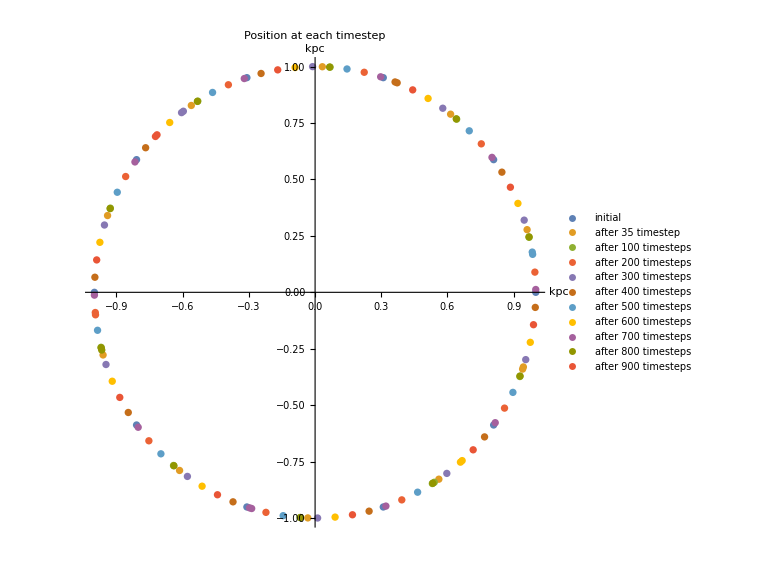

```mathematica
ch2posgraph = ListPlot[{ch2pos1,ch2pos35,ch2pos100,ch2pos300,ch2pos400,ch2pos500,ch2pos600,ch2pos700,ch2pos800,ch2pos900,ch2pos1000},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"initial","after 35 timestep","after 100 timesteps","after 200 timesteps","after 300 timesteps","after 400 timesteps","after 500 timesteps","after 600 timesteps","after 700 timesteps", "after 800 timesteps","after 900 timesteps","after 1000 timestes"},AxesLabel->{"kpc","kpc"}, PlotLabel->"Position at each timestep"]
```

#### Velocity Dispersion

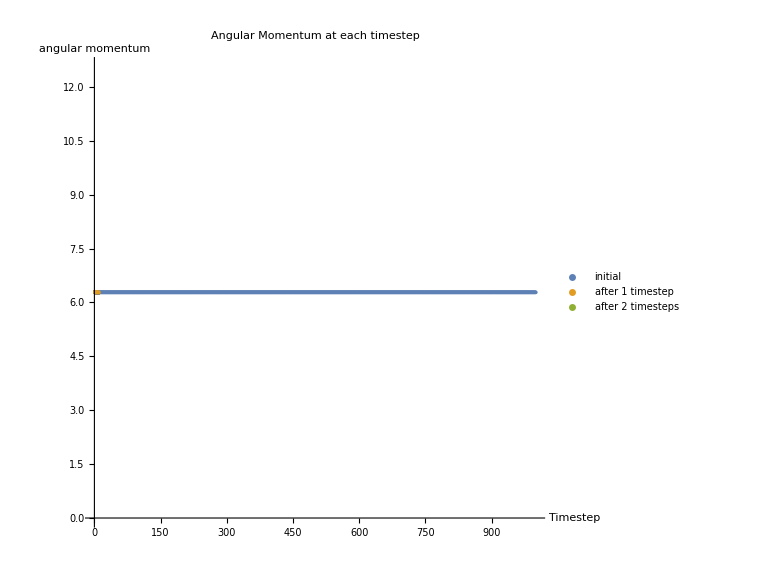

```mathematica
ch2AMgraph = ListPlot[{ch2AM,ch2AM1,ch2AM2,ch2AM3,ch2AM4,ch2AM5,ch2AM6,ch2AM7,ch2AM8,ch2AM9,ch2AM10,ch2AM11,ch2AM12,ch2AM13,ch2AM14,ch2AM15,ch2AM16,ch2AM17,ch2AM18,ch2AM19,ch2AM20,ch2AM100,ch2AM200,ch2AM300,ch2AM400,ch2AM500,ch2AM600,ch2AM700,ch2AM700,ch2AM800,ch2AM900,ch2AM1000},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"initial","after 1 timestep","after 2 timesteps"},AxesLabel->{"Timestep
","angular momentum"}, PlotLabel-> "Angular Momentum at each timestep"]
```

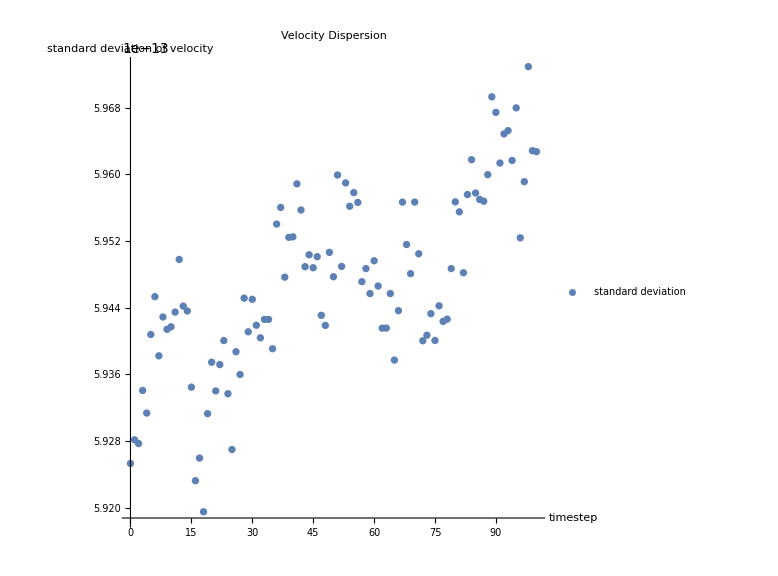

```mathematica
ch2SDgraph = ListPlot[{ch1SD},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"standard deviation"},AxesLabel->{"timestep","standard deviation of velocity"}, PlotLabel-> "Velocity Dispersion"]
```

#### Power Spectra

```mathematica
ch2PS1 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",1,1;;4}];
ch2PS2 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",2,1;;4}];
ch2PS3 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",3,1;;4}];
ch2PS4 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",4,1;;4}];
ch2PS5 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",5,1;;4}];
ch2PS6 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",6,1;;4}];
ch2PS7 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",7,1;;4}];
ch2PS8 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",8,1;;4}];
ch2PS9 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",9,1;;4}];
ch2PS10 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",10,1;;4}];
ch2PS11 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",11,1;;4}];
ch2PS12 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",12,1;;4}];
ch2PS13 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",13,1;;4}];
ch2PS14 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",14,1;;4}];
ch2PS15 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",15,1;;4}];
ch2PS16 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",16,1;;4}];
ch2PS17 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",17,1;;4}];
ch2PS18 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",18,1;;4}];
ch2PS19 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",19,1;;4}];
ch2PS20 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",20,1;;4}];
ch2PS21 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",21,1;;4}];
ch2PS81 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",81,1;;4}];
ch2PS82 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",82,1;;4}];
ch2PS83 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",83,1;;4}];
ch2PS84 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",84,1;;4}];
ch2PS85 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",85,1;;4}];
ch2PS86 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",86,1;;4}];
ch2PS87 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",87,1;;4}];
ch2PS88 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",88,1;;4}];
ch2PS89 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",89,1;;4}];
ch2PS90 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",90,1;;4}];
ch2PS91 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",91,1;;4}];
ch2PS92 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",92,1;;4}];
ch2PS93 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",93,1;;4}];
ch2PS94 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",94,1;;4}];
ch2PS95 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",95,1;;4}];
ch2PS96 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",96,1;;4}];
ch2PS97 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",97,1;;4}];
ch2PS98 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",98,1;;4}];
ch2PS99 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",99,1;;4}];
ch2PS100 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",100,1;;4}];
ch2PS200 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",200,1;;4}];
ch2PS300 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",300,1;;4}];
ch2PS400 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",400,1;;4}];
ch2PS500 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",500,1;;4}];
ch2PS600 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",600,1;;4}];
ch2PS700 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",700,1;;4}];
ch2PS800 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",800,1;;4}];
ch2PS900 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",900,1;;4}];
ch2PS1000 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/PS2.csv",{"Data",1000,1;;4}];
```

```mathematica
ch2FT1 = Abs[Fourier[{ch2PS1}]]^2;
ch2FT2 = Abs[Fourier[{ch2PS2}]]^2;
ch2FT3 = Abs[Fourier[{ch2PS3}]]^2;
ch2FT4 = Abs[Fourier[{ch2PS4}]]^2;
ch2FT5 = Abs[Fourier[{ch2PS5}]]^2;
ch2FT6 = Abs[Fourier[{ch2PS6}]]^2;
ch2FT7 = Abs[Fourier[{ch2PS7}]]^2;
ch2FT8 = Abs[Fourier[{ch2PS8}]]^2;
ch2FT9 = Abs[Fourier[{ch2PS9}]]^2;
ch2FT10 = Abs[Fourier[{ch2PS10}]]^2;
ch2FT11 = Abs[Fourier[{ch2PS11}]]^2;
ch2FT12 = Abs[Fourier[{ch2PS12}]]^2;
ch2FT13 = Abs[Fourier[{ch2PS13}]]^2;
ch2FT14 = Abs[Fourier[{ch2PS14}]]^2;
ch2FT15 = Abs[Fourier[{ch2PS15}]]^2;
ch2FT16 = Abs[Fourier[{ch2PS16}]]^2;
ch2FT17 = Abs[Fourier[{ch2PS17}]]^2;
ch2FT18 = Abs[Fourier[{ch2PS18}]]^2;
ch2FT19 = Abs[Fourier[{ch2PS19}]]^2;
ch2FT20 = Abs[Fourier[{ch2PS20}]]^2;
ch2FT81 = Abs[Fourier[{ch2PS81}]]^2;
ch2FT82 = Abs[Fourier[{ch2PS82}]]^2;
ch2FT83 = Abs[Fourier[{ch2PS83}]]^2;
ch2FT84 = Abs[Fourier[{ch2PS84}]]^2;
ch2FT85 = Abs[Fourier[{ch2PS85}]]^2;
ch2FT86 = Abs[Fourier[{ch2PS86}]]^2;
ch2FT87 = Abs[Fourier[{ch2PS87}]]^2;
ch2FT88 = Abs[Fourier[{ch2PS88}]]^2;
ch2FT89 = Abs[Fourier[{ch2PS89}]]^2;
ch2FT90 = Abs[Fourier[{ch2PS90}]]^2;
ch2FT91 = Abs[Fourier[{ch2PS91}]]^2;
ch2FT92 = Abs[Fourier[{ch2PS92}]]^2;
ch2FT93 = Abs[Fourier[{ch2PS93}]]^2;
ch2FT94 = Abs[Fourier[{ch2PS94}]]^2;
ch2FT95 = Abs[Fourier[{ch2PS95}]]^2;
ch2FT96 = Abs[Fourier[{ch2PS96}]]^2;
ch2FT97 = Abs[Fourier[{ch2PS97}]]^2;
ch2FT98 = Abs[Fourier[{ch2PS98}]]^2;
ch2FT99 = Abs[Fourier[{ch2PS99}]]^2;
ch2FT100 = Abs[Fourier[{ch2PS100}]]^2;
ch2FT200 = Abs[Fourier[{ch2PS100}]]^2;
ch2FT300 = Abs[Fourier[{ch2PS100}]]^2;
ch2FT400 = Abs[Fourier[{ch2PS100}]]^2;
ch2FT500 = Abs[Fourier[{ch2PS100}]]^2;
ch2FT600 = Abs[Fourier[{ch2PS100}]]^2;
ch2FT700 = Abs[Fourier[{ch2PS100}]]^2;
ch2FT800 = Abs[Fourier[{ch2PS100}]]^2;
ch2FT900 = Abs[Fourier[{ch2PS100}]]^2;
ch2FT1000 = Abs[Fourier[{ch2PS100}]]^2;

ch2PSgraph =  ListLinePlot[{ch2FT1},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"initial","after 1 timestep","after 2 timesteps"},AxesLabel->{"particle number","angular momentum"}, PlotLabel-> "Power Spectra"]
```

{{6.25,0.,0.25,0.}}

-Graphics-

### Version 3: Leapfrog with triaxiality (dimensionless units) NFW parameters = {417.0 * pow(10,3) * mau * secyr, 36.54 * kpcau, 90.0 * pi / 180, 1.0, 1.0, 0.8} 10 test particles r0 = 15 kpc 1000 timesteps of 1,000, 000 years each

#### Coordinates:

```mathematica
ch3pos1 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test3.csv",{"Data",1;;10,6;;7}];
ch3pos2 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test3.csv",{"Data",10;;20,6;;7}];
ch3pos3 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test3.csv",{"Data",20;;30,6;;7}];
ch3pos4 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test3.csv",{"Data",30;;40,6;;7}];
ch3pos5 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test3.csv",{"Data",40;;50,6;;7}];
ch3pos6 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test3.csv",{"Data",50;;60,6;;7}];
ch3pos7 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test3.csv",{"Data",60;;70,6;;7}];
ch3pos8 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test3.csv",{"Data",70;;80,6;;7}];
ch3pos9 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test3.csv",{"Data",80;;90,6;;7}];
ch3pos10 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test3.csv",{"Data",90;;100,6;;7}];
ch3pos11 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test3.csv",{"Data",100;;110,6;;7}];
ch3pos12 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test3.csv",{"Data",110;;120,6;;7}];
ch3pos13 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test3.csv",{"Data",120;;130,6;;7}];
ch3pos14 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test3.csv",{"Data",130;;140,6;;7}];
ch3pos15 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test3.csv",{"Data",140;;150,6;;7}];
ch3pos16 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test3.csv",{"Data",150;;160,6;;7}];
ch3pos17 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test3.csv",{"Data",160;;170,6;;7}];
ch3pos18 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test3.csv",{"Data",170;;180,6;;7}];
ch3pos19 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test3.csv",{"Data",180;;190,6;;7}];
ch3pos20 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test3.csv",{"Data",190;;200,6;;7}];
ch3pos21 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test3.csv",{"Data",200;;210,6;;7}];
ch3pos22 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test3.csv",{"Data",210;;220,6;;7}];
ch3pos23 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test3.csv",{"Data",220;;230,6;;7}];
ch3pos24 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test3.csv",{"Data",230;;240,6;;7}];
ch3pos25 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test3.csv",{"Data",240;;250,6;;7}];
ch3pos26 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test3.csv",{"Data",250;;260,6;;7}];
ch3pos27 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test3.csv",{"Data",260;;270,6;;7}];
ch3pos28 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test3.csv",{"Data",270;;280,6;;7}];
ch3pos29 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test3.csv",{"Data",280;;290,6;;7}];
ch3pos30 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test3.csv",{"Data",290;;300,6;;7}];
ch3pos31 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test3.csv",{"Data",300;;310,6;;7}];
ch3pos32 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test3.csv",{"Data",310;;320,6;;7}];
ch3pos33 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test3.csv",{"Data",320;;330,6;;7}];
ch3pos34 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test3.csv",{"Data",330;;340,6;;7}];
ch3pos35 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test3.csv",{"Data",340;;350,6;;7}];
ch3pos36 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test3.csv",{"Data",350;;360,6;;7}];
ch3pos100 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test3.csv",{"Data",990;;1000,6;;7}];
ch3pos200 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test3.csv",{"Data",1990;;2000,6;;7}];
ch3pos300 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test3.csv",{"Data",2990;;3000,6;;7}];
ch3pos400 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test3.csv",{"Data",3990;;4000,6;;7}];
ch3pos500 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test3.csv",{"Data",4990;;5000,6;;7}];
ch3pos600 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test3.csv",{"Data",5990;;6000,6;;7}];
ch3pos700 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test3.csv",{"Data",6990;;7000,6;;7}];
ch3pos800 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test3.csv",{"Data",7990;;8000,6;;7}];
ch3pos900 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test3.csv",{"Data",8990;;9000,6;;7}];
ch3pos1000 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test3.csv",{"Data",9990;;10000,6;;7}];

ch3vel1 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test3.csv",{"Data",1;;10,4;;5}]

ch3AM1 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",1,1;;10}];
ch3AM2 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",2,1;;10}];
ch3AM3 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",3,1;;10}]; 
ch3AM100 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM3.csv",{"Data",100,1;;10}];
ch3AM200 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM3.csv",{"Data",200,1;;10}];
ch3AM300 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM3.csv",{"Data",300,1;;10}];
ch3AM400 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM3.csv",{"Data",400,1;;10}];
ch3AM500 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM3.csv",{"Data",500,1;;10}];
ch3AM600 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM3.csv",{"Data",600,1;;10}];
ch3AM700 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM3.csv",{"Data",700,1;;10}];
ch3AM800 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM3.csv",{"Data",800,1;;10}];
ch3AM900 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM3.csv",{"Data",900,1;;10}];
ch3AM1000 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM3.csv",{"Data",1000,1;;10}];
(*since all angular momentums are same at each timestep, import just one column to see how it changes for every particle over time*)
ch3AM = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM2.csv",{"Data",1;;1000,1}];

ch3SD = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/SD3.csv",{"Data",1;;1000,1;;2}];
ch3SD6000 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/SD3.csv",{"Data",6000,1;;2}];
```

{{6.28319,1.},{6.28319,1.},{6.28319,1.},{6.28319,1.},{6.28319,1.},{6.28319,1.},{6.28319,1.},{6.28319,1.},{6.28319,1.},{6.28319,1.}}

Import::noelem: The Import element "6000" is not present when importing as CSV.

```mathematica
{{12.1373,8.81829},{4.63605,14.2683},{-4.63605,14.2683},{-12.1373,8.81829},{-15.0026,1.83728*^-15},{-12.1373,-8.81829},{-4.63605,-14.2683},{4.63605,-14.2683},{12.1373,-8.81829},{15.0026,-3.67457*^-15}}
Sqrt[12.1373^2 + 8.81829^2]
```

{{12.1373,8.81829},{4.63605,14.2683},{-4.63605,14.2683},{-12.1373,8.81829},{-15.0026,1.83728×10^-15},{-12.1373,-8.81829},{-4.63605,-14.2683},{4.63605,-14.2683},{12.1373,-8.81829},{15.0026,-3.67457×10^-15}}

15.0025

#### Position

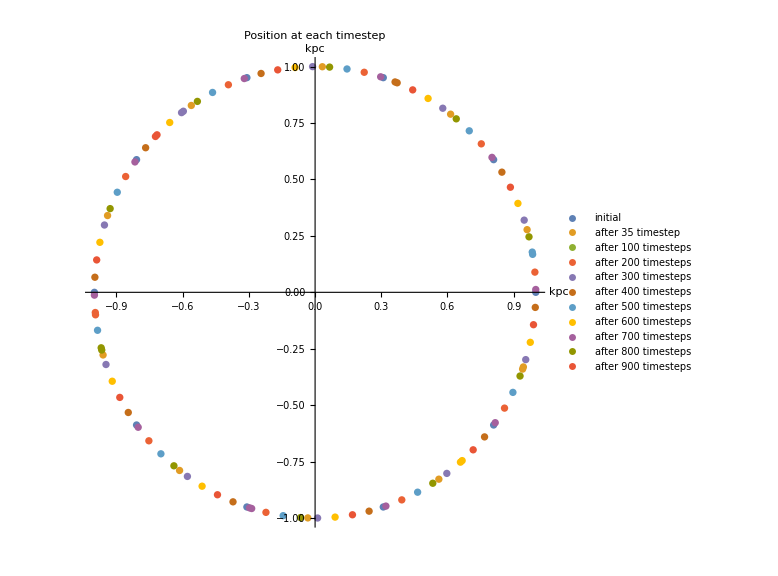

```mathematica
ch3posgraph = ListPlot[{ch3pos1,ch3pos35,ch3pos100，ch3pos200,ch3pos300,ch3pos400,ch3pos500,ch3pos600,ch3pos700,ch3pos800,ch3pos900,ch3pos1000},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"initial","after 35 timestep","after 100 timesteps","after 200 timesteps","after 300 timesteps","after 400 timesteps","after 500 timesteps","after 600 timesteps","after 700 timesteps","after 800 timesteps","after 900 timesteps","after 1000 timesteps","after 1000 timesteps"},AxesLabel->{"kpc","kpc"}, PlotLabel->"Position at each timestep"]
```

#### Velocity Dispersion

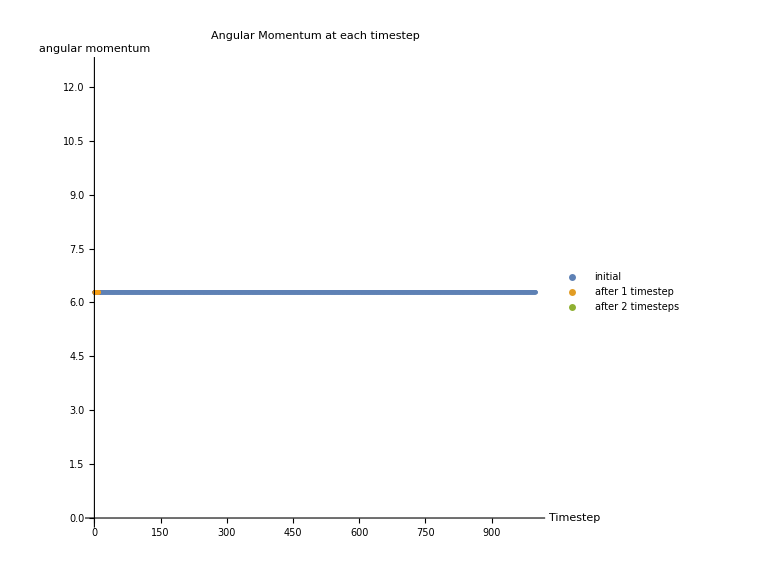

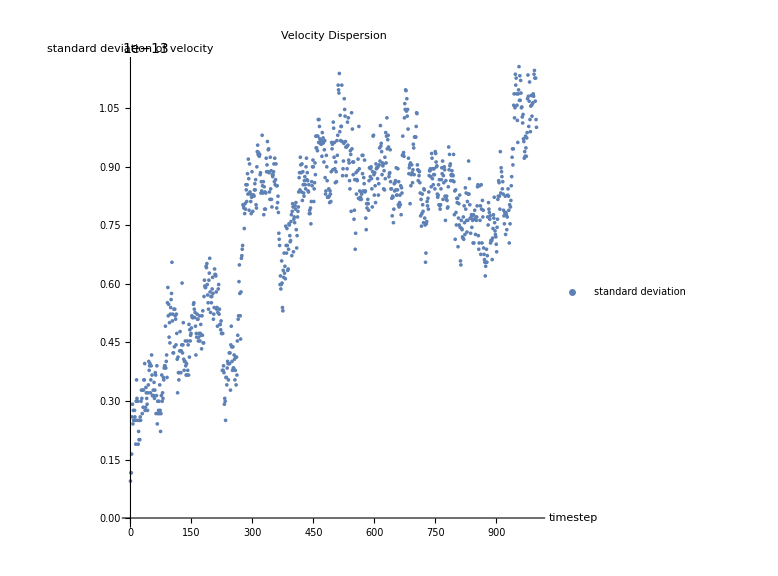

```mathematica
ch3AMgraph = ListPlot[{ch3AM,ch3AM1,ch3AM100,ch3AM200,ch3AM300,ch3AM400,ch3AM500,ch3AM600,ch3AM700,ch3AM700,ch3AM800,ch3AM900,ch3AM1000},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"initial","after 1 timestep","after 2 timesteps"},AxesLabel->{"Timestep
","angular momentum"}, PlotLabel-> "Angular Momentum at each timestep"]
ch3SDgraph = ListPlot[{ch3SD,ch3SD6000},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"standard deviation"},AxesLabel->{"timestep","standard deviation of velocity"}, PlotLabel-> "Velocity Dispersion"]
```

### Version 4: Leapfrog with triaxiality (dimensionless units) NFW parameters = {417.0 * pow(10,3) * mau * secyr, 36.54 * kpcau, 90.0 * pi / 180, 1.0, 1.0, 0.8} 10 test particles r0 = 15 kpc 6000 timesteps of 1,000,000 years each

#### Coordinates

```mathematica
ch4pos1 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test4.csv",{"Data",1;;10,6;;7}];
ch4pos2 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test4.csv",{"Data",10;;20,6;;7}];
ch4pos3 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test4.csv",{"Data",20;;30,6;;7}];
ch4pos4 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test4.csv",{"Data",30;;40,6;;7}];
ch4pos5 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test4.csv",{"Data",40;;50,6;;7}];
ch4pos6 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test4.csv",{"Data",50;;60,6;;7}];
ch4pos7 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test4.csv",{"Data",60;;70,6;;7}];
ch4pos8 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test4.csv",{"Data",70;;80,6;;7}];
ch4pos9 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test4.csv",{"Data",80;;90,6;;7}];
ch4pos10 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test4.csv",{"Data",90;;100,6;;7}];
ch4pos11 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test4.csv",{"Data",100;;110,6;;7}];
ch4pos12 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test4.csv",{"Data",110;;120,6;;7}];
ch4pos13 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test4.csv",{"Data",120;;130,6;;7}];
ch4pos14 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test4.csv",{"Data",130;;140,6;;7}];
ch4pos15 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test4.csv",{"Data",140;;150,6;;7}];
ch4pos16 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test4.csv",{"Data",150;;160,6;;7}];
ch4pos17 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test4.csv",{"Data",160;;170,6;;7}];
ch4pos18 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test4.csv",{"Data",170;;180,6;;7}];
ch4pos19 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test4.csv",{"Data",180;;190,6;;7}];
ch4pos20 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test4.csv",{"Data",190;;200,6;;7}];
ch4pos21 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test4.csv",{"Data",200;;210,6;;7}];
ch4pos22 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test4.csv",{"Data",210;;220,6;;7}];
ch4pos23 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test4.csv",{"Data",220;;230,6;;7}];
ch4pos24 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test4.csv",{"Data",230;;240,6;;7}];
ch4pos25 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test4.csv",{"Data",240;;250,6;;7}];
ch4pos26 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test4.csv",{"Data",250;;260,6;;7}];
ch4pos27 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test4.csv",{"Data",260;;270,6;;7}];
ch4pos28 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test4.csv",{"Data",270;;280,6;;7}];
ch4pos29 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test4.csv",{"Data",280;;290,6;;7}];
ch4pos30 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test4.csv",{"Data",290;;300,6;;7}];
ch4pos31 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test4.csv",{"Data",300;;310,6;;7}];
ch4pos32 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test4.csv",{"Data",310;;320,6;;7}];
ch4pos33 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test4.csv",{"Data",320;;330,6;;7}];
ch4pos34 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test4.csv",{"Data",330;;340,6;;7}];
ch4pos35 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test4.csv",{"Data",340;;350,6;;7}];
ch4pos36 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test4.csv",{"Data",350;;360,6;;7}];
ch4pos1000 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test4.csv",{"Data",9990;;10000,6;;7}];
ch4pos2000 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test4.csv",{"Data",19990;;20000,6;;7}];
ch4pos3000 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test4.csv",{"Data",29990;;30000,6;;7}];
ch4pos4000 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test4.csv",{"Data",39990;;40000,6;;7}];
ch4pos5000 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test4.csv",{"Data",49990;;50000,6;;7}];
ch4pos6000 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test4.csv",{"Data",59990;;60000,6;;7}];

ch4AM1 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM4.csv",{"Data",1,1;;10}];
ch4AM2 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM4.csv",{"Data",2,1;;10}];
ch4AM3 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM4.csv",{"Data",3,1;;10}]; 
ch4AM1000= Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM4.csv",{"Data",1000,1;;10}];
ch4AM2000 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM4.csv",{"Data",2000,1;;10}];
ch4AM3000 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM4.csv",{"Data",3000,1;;10}];
ch4AM4000 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM4.csv",{"Data",4000,1;;10}];
ch4AM5000 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM4.csv",{"Data",5000,1;;10}];
ch4AM6000 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM4.csv",{"Data",6000,1;;10}];
(*since all angular momentums are same at each timestep, import just one column to see how it changes for every particle over time*)
ch4AM = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM4.csv",{"Data",1;;1000,1}];

(*SD with units*)
ch4SD = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/SD4.csv",{"Data",1;;6000,1;;2}];
 
ch4magforce = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test4.csv",{"Data",1;;60000,3}];
```

#### Position

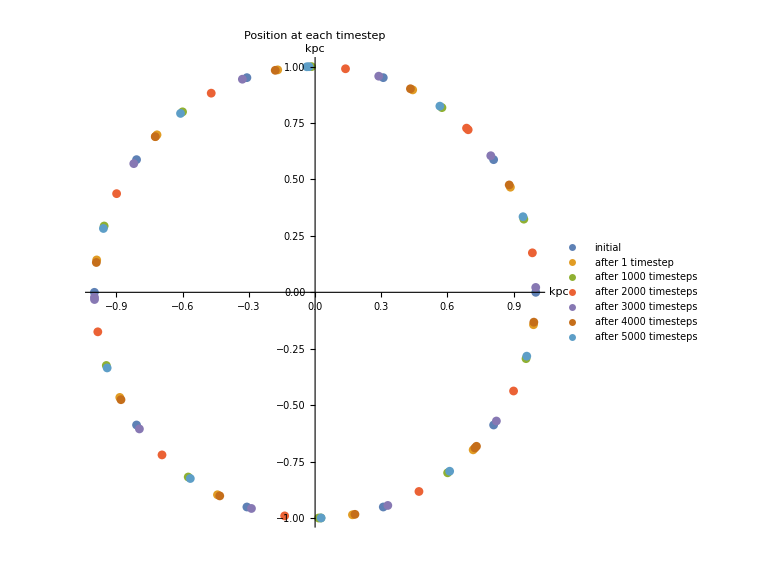

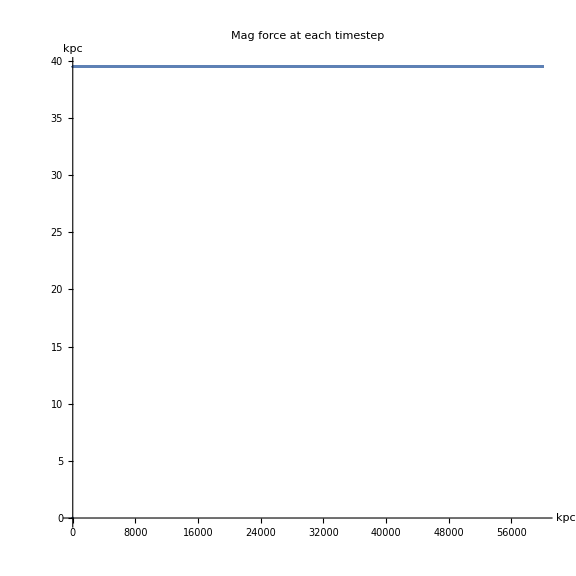

```mathematica
ch4posgraph = ListPlot[{ch4pos1,ch4pos1000,ch4pos2000,ch4pos3000,ch4pos4000,ch4pos5000,ch4pos6000},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"initial","after 1 timestep","after 1000 timesteps","after 2000 timesteps","after 3000 timesteps","after 4000 timesteps","after 5000 timesteps","after 6000 timesteps"},AxesLabel->{"kpc","kpc"}, PlotLabel->"Position at each timestep"]
ch4posgraph = ListPlot[{ch4magforce},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,AxesLabel->{"kpc","kpc"}, PlotLabel->"Mag force at each timestep"]
```

#### Velocity Dispersion

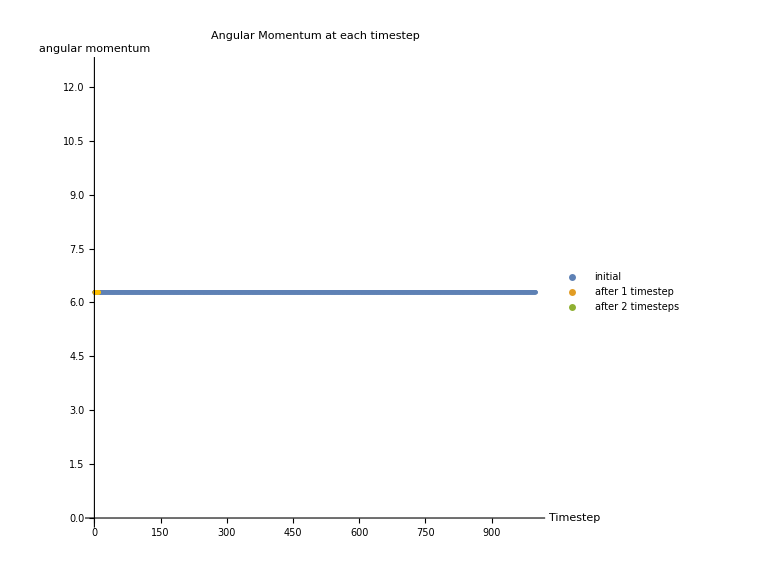

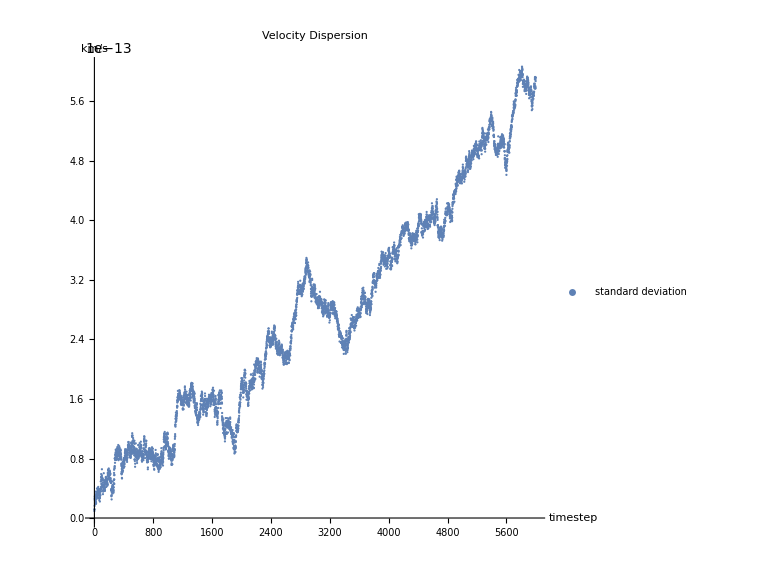

```mathematica
ch4AMgraph = ListPlot[{ch4AM,ch4AM1,ch4AM1000,ch4AM2000,ch4AM3000,ch4AM4000,ch4AM5000,ch4AM6000},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"initial","after 1 timestep","after 2 timesteps"},AxesLabel->{"Timestep
","angular momentum"}, PlotLabel-> "Angular Momentum at each timestep"]
ch4SDgraph = ListPlot[{ch4SD},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"standard deviation"},AxesLabel->{"timestep","km/s"}, PlotLabel-> "Velocity Dispersion"]
```

### Version 5: Leapfrog with more triaxiality (dimensionless units) NFW parameters = {417 * pow(10,3) * mau * secyr, 36.54 * kpcau, 90.0 * pi / 180, 0.95, 1.0, 0.8} 10 test particles r0 = 15 kpc 6000 timesteps of 1,000, 000 years each

#### Coordinates

```mathematica
ch5pos1 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test5.csv",{"Data",1;;10,6;;7}];
ch5pos2 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test5.csv",{"Data",10;;20,6;;7}];
ch5pos3 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test5.csv",{"Data",20;;30,6;;7}];
ch5pos4 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test5.csv",{"Data",30;;40,6;;7}];
ch5pos5 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test5.csv",{"Data",40;;50,6;;7}];
ch5pos6 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test5.csv",{"Data",50;;60,6;;7}];
ch5pos7 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test5.csv",{"Data",60;;70,6;;7}];
ch5pos8 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test5.csv",{"Data",70;;80,6;;7}];
ch5pos9 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test5.csv",{"Data",80;;90,6;;7}];
ch5pos10 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test5.csv",{"Data",90;;100,6;;7}];
ch5pos11 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test5.csv",{"Data",100;;110,6;;7}];
ch5pos12 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test5.csv",{"Data",110;;120,6;;7}];
ch5pos13 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test5.csv",{"Data",120;;130,6;;7}];
ch5pos14 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test5.csv",{"Data",130;;140,6;;7}];
ch5pos15 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test5.csv",{"Data",140;;150,6;;7}];
ch5pos16 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test5.csv",{"Data",150;;160,6;;7}];
ch5pos17 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test5.csv",{"Data",160;;170,6;;7}];
ch5pos18 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test5.csv",{"Data",170;;180,6;;7}];
ch5pos19 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test5.csv",{"Data",180;;190,6;;7}];
ch5pos20 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test5.csv",{"Data",190;;200,6;;7}];
ch5pos21 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test5.csv",{"Data",200;;210,6;;7}];
ch5pos22 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test5.csv",{"Data",210;;220,6;;7}];
ch5pos23 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test5.csv",{"Data",220;;230,6;;7}];
ch5pos24 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test5.csv",{"Data",230;;240,6;;7}];
ch5pos25 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test5.csv",{"Data",240;;250,6;;7}];
ch5pos26 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test5.csv",{"Data",250;;260,6;;7}];
ch5pos27 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test5.csv",{"Data",260;;270,6;;7}];
ch5pos28 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test5.csv",{"Data",270;;280,6;;7}];
ch5pos29 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test5.csv",{"Data",280;;290,6;;7}];
ch5pos30 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test5.csv",{"Data",290;;300,6;;7}];
ch5pos31 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test5.csv",{"Data",300;;310,6;;7}];
ch5pos32 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test5.csv",{"Data",310;;320,6;;7}];
ch5pos33 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test5.csv",{"Data",320;;330,6;;7}];
ch5pos34 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test5.csv",{"Data",330;;340,6;;7}];
ch5pos35 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test5.csv",{"Data",340;;350,6;;7}];
ch5pos36 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test5.csv",{"Data",350;;360,6;;7}];
ch5pos100 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test5.csv",{"Data",990;;1000,6;;7}];
ch5pos1000 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test5.csv",{"Data",9990;;10000,6;;7}];
ch5pos2000 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test5.csv",{"Data",19990;;20000,6;;7}];
ch5pos3000 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test5.csv",{"Data",29990;;30000,6;;7}];
ch5pos4000 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test5.csv",{"Data",39990;;40000,6;;7}];
ch5pos5000 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test5.csv",{"Data",49990;;50000,6;;7}];
ch5pos6000 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test5.csv",{"Data",59990;;60000,6;;7}];

ch5AM1 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM5.csv",{"Data",1,1;;10}];
ch5AM2 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM5.csv",{"Data",2,1;;10}];
ch5AM3 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM5.csv",{"Data",3,1;;10}]; 
ch5AM1000 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM5.csv",{"Data",1000,1;;10}];
ch5AM2000 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM5.csv",{"Data",2000,1;;10}];
ch5AM3000 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM5.csv",{"Data",3000,1;;10}];
ch5AM4000 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM5.csv",{"Data",4000,1;;10}];
ch5AM5000 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM5.csv",{"Data",5000,1;;10}];
ch5AM6000 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM5.csv",{"Data",6000,1;;10}];
(*since all angular momentums are same at each timestep, import just one column to see how it changes for every particle over time*)
ch5AM = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM5.csv",{"Data",1;;6000,1}];

(*SD with units*)
ch5SD = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/SD5.csv",{"Data",1;;6000,1;;2}];
```

#### Position

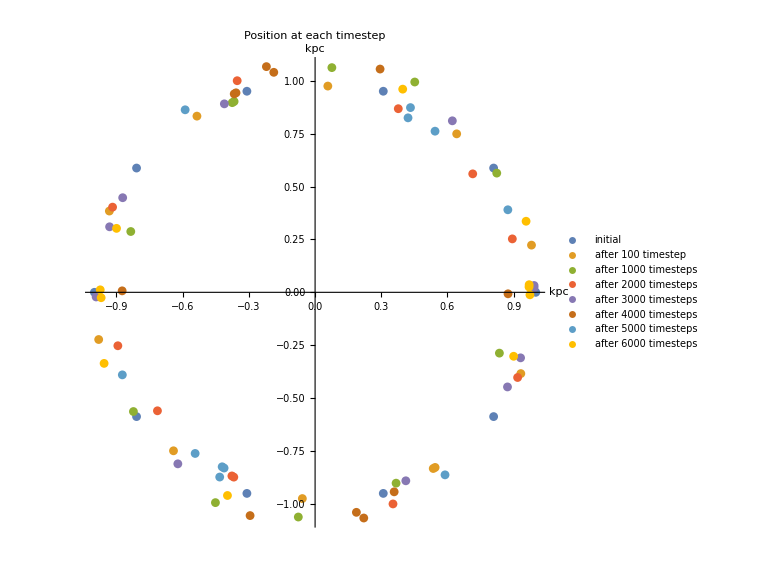

```mathematica
ch5posgraph = ListPlot[{ch5pos1,ch5pos100,ch5pos1000,ch5pos2000,ch5pos3000,ch5pos4000,ch5pos5000,ch5pos6000},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"initial","after 100 timestep","after 1000 timesteps","after 2000 timesteps","after 3000 timesteps","after 4000 timesteps","after 5000 timesteps","after 6000 timesteps"},AxesLabel->{"kpc","kpc"}, PlotLabel->"Position at each timestep"]
```

#### Velocity Dispersion

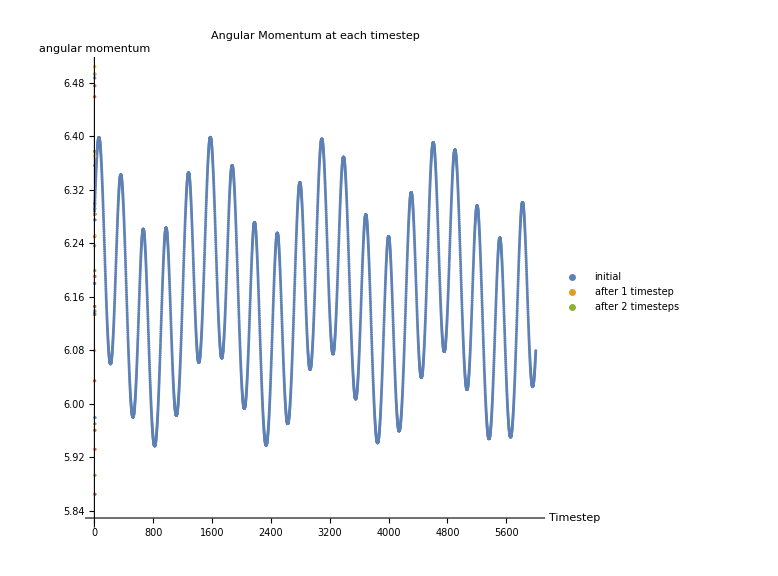

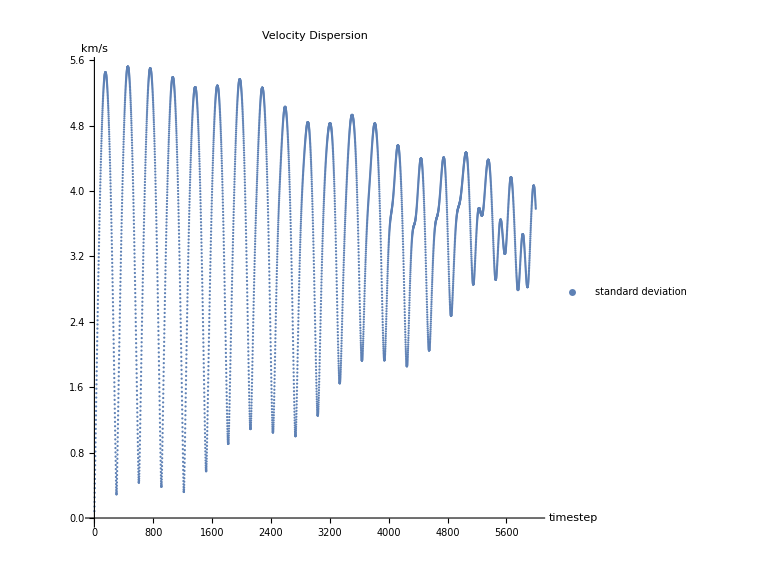

```mathematica
ch5AMgraph = ListPlot[{ch5AM,ch5AM1,ch5AM1000,ch5AM2000,ch5AM3000,ch5AM4000,ch5AM5000,ch5AM6000},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"initial","after 1 timestep","after 2 timesteps"},AxesLabel->{"Timestep
","angular momentum"}, PlotLabel-> "Angular Momentum at each timestep"]
ch5SDgraph = ListPlot[{ch5SD},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"standard deviation"},AxesLabel->{"timestep","km/s"}, PlotLabel-> "Velocity Dispersion"]
```

### Version 6: Leapfrog with different halo (dimensionless units) NFW parameters = {200.0* kmkpc, 10.0 , 90.0 * pi / 180, 1.0, 1.0, 1.0} 10 test particles r0 = 15 kpcs 10 timesteps of 1000000 years each

#### Coordinates

```mathematica
ch6pos1 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test6.csv",{"Data",1;;10,6;;7}];
ch6pos1000 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test6.csv",{"Data",9990;;10000,6;;7}];
ch6pos2000 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test6.csv",{"Data",19990;;20000,6;;7}];
ch6pos3000 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test6.csv",{"Data",29990;;30000,6;;7}];
ch6pos4000 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test6.csv",{"Data",39990;;40000,6;;7}];
ch6pos5000 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test6.csv",{"Data",49990;;50000,6;;7}];
ch6pos6000 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test6.csv",{"Data",59990;;60000,6;;7}];

ch6AM1000 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM6.csv",{"Data",1000,1;;10}];
ch6AM2000 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM6.csv",{"Data",2000,1;;10}];
ch6AM3000 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM6.csv",{"Data",3000,1;;10}];
ch6AM4000 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM6.csv",{"Data",4000,1;;10}];
ch6AM5000 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM6.csv",{"Data",5000,1;;10}];
ch6AM6000 = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM6.csv",{"Data",6000,1;;10}];
ch6AM = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM6.csv",{"Data",1;;6000,1}];

(*SD with units*)
ch6SD = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/SD6.csv",{"Data",1;;6000,1;;2}];
```

#### Position

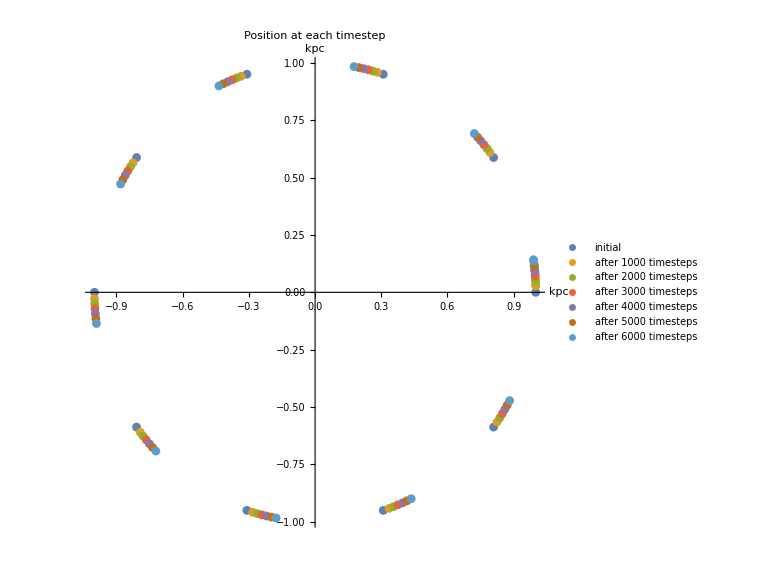

```mathematica
ch6posgraph = ListPlot[{ch6pos1,ch6pos1000,ch6pos2000,ch6pos3000,ch6pos4000,ch6pos5000,ch6pos6000},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"initial","after 1000 timesteps","after 2000 timesteps","after 3000 timesteps","after 4000 timesteps","after 5000 timesteps","after 6000 timesteps"},AxesLabel->{"kpc","kpc"}, PlotLabel->"Position at each timestep"]
```

#### Velocity Dispersion

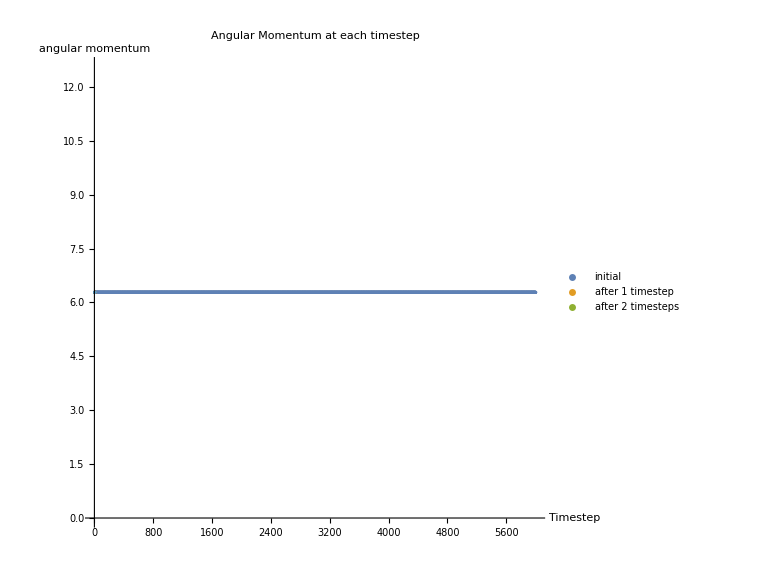

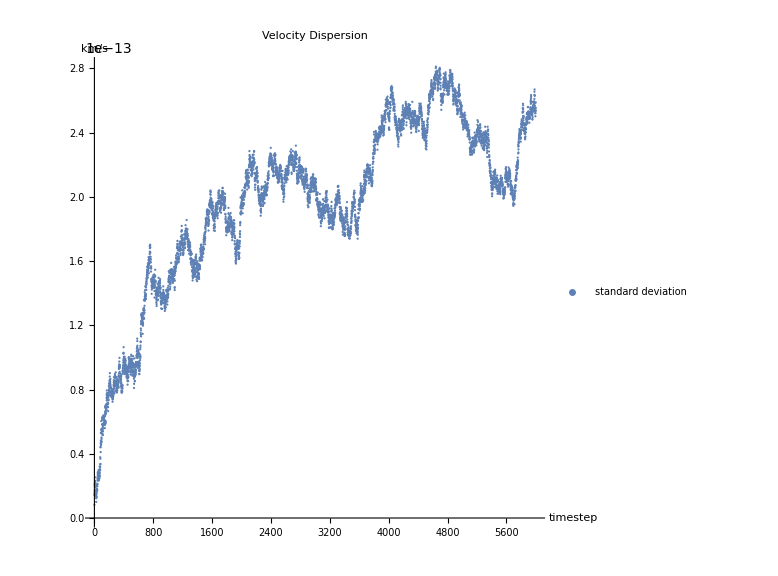

```mathematica
ch6AMgraph = ListPlot[{ch6AM,ch6AM1000,ch6AM2000,ch6AM3000,ch6AM4000,ch6AM5000,ch6AM6000},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"initial","after 1 timestep","after 2 timesteps"},AxesLabel->{"Timestep
","angular momentum"}, PlotLabel-> "Angular Momentum at each timestep"]
ch6SDgraph = ListPlot[{ch6SD},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"standard deviation"},AxesLabel->{"timestep","km/s"}, PlotLabel-> "Velocity Dispersion"]
```

### Version 7: dot products in dimensionless units, without leapfrog (position and velocity output with units) NFW parameters = {417.0 * pow(10,3) * mau * secyr, 36.54 , 90.0 * pi / 180, 1.0, 1.0, 1.0} (NO TRIAXIALITY) 1 test particle r0 = 15 kpc 10 timesteps of 1000000 years each switched order of updating position and velocity (updates velocity first)

```mathematica
ch7dotposvel = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test7.csv",{"Data",1;;12,1}];
ch7dotforcevel = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test7.csv",{"Data",1;;12,2}];
ch7magforce = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test7.csv",{"Data",1;;12,3}];
ch7magvel = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test7.csv",{"Data",1;;12,4}];
ch7magpos = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test7.csv",{"Data",1;;12,5}];
ch7pos = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test7.csv",{"Data",1;;12,6;;7}];
ch7vel = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test7.csv",{"Data",1;;12,9;;10}];
```

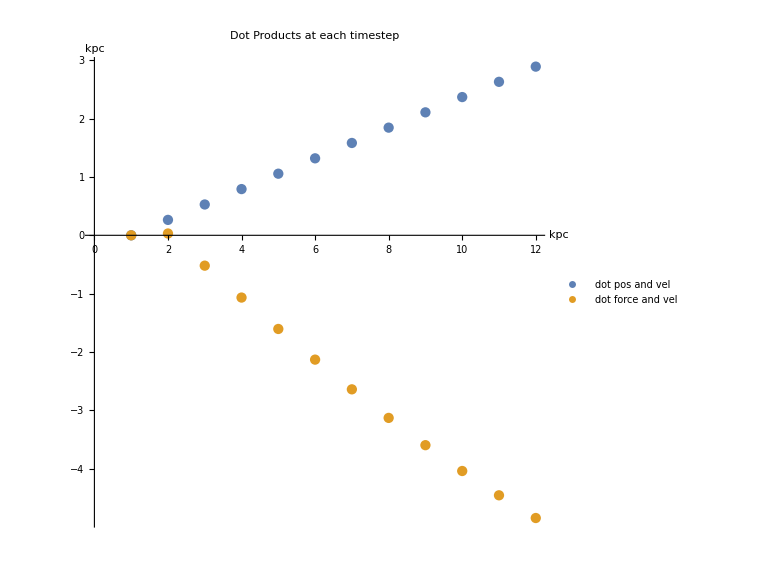

```mathematica
ch7dotgraph = ListPlot[{ch7dotposvel,ch7dotforcevel},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"dot pos and vel","dot force and vel"},AxesLabel->{"kpc","kpc"}, PlotLabel->"Dot Products at each timestep"]
```

### Version 8: dot products in dimensionless units, without leapfrog NFW parameters = {417.0 * pow(10,3) * mau * secyr, 36.54 , 90.0 * pi / 180, 1.0, 1.0, 1.0} (NO TRIAXIALITY) 1 test particle r0 = 15 kpc 1000 timesteps of 1000000 years each

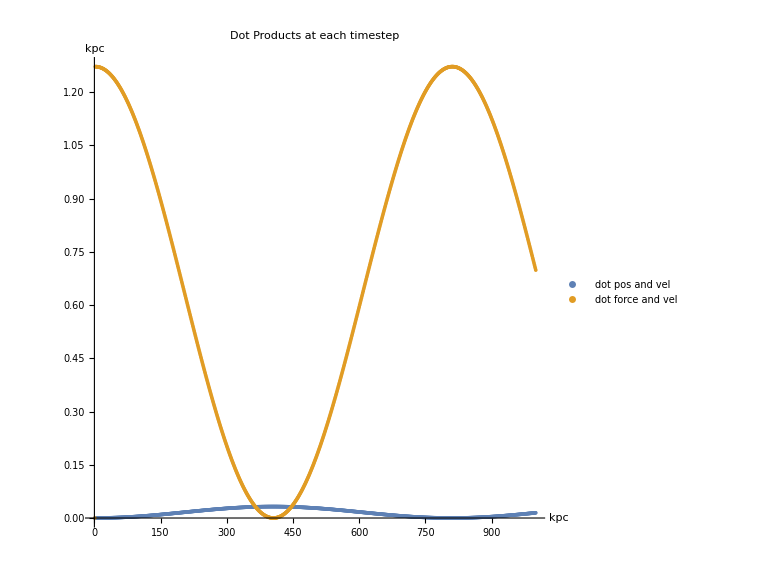

```mathematica
ch8dotposvel = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test8.csv",{"Data",1;;1000,1}];
ch8dotforcevel = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test8.csv",{"Data",1;;1000,2}];
ch8magforce = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test8.csv",{"Data",1;;1000,3}];
ch8magvel = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test8.csv",{"Data",1;;1000,4}];
ch8magpos = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test8.csv",{"Data",1;;1000,5}];
ch8pos = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test8.csv",{"Data",1;;1000,6;;7}];
ch8vel = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test8.csv",{"Data",1;;1000,9;;10}];


ch8dotgraph = ListPlot[{ch8dotposvel,ch8dotforcevel},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"dot pos and vel","dot force and vel"},AxesLabel->{"kpc","kpc"}, PlotLabel->"Dot Products at each timestep"]
```

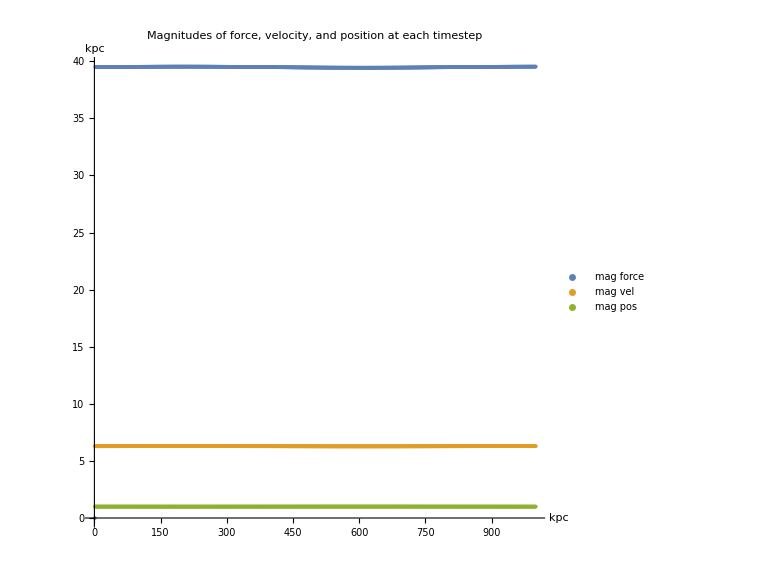

```mathematica
ch8maggraph = ListPlot[{ch8magforce,ch8magvel,ch8magpos},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"mag force","mag vel","mag pos"},AxesLabel->{"kpc","kpc"}, PlotLabel->"Magnitudes of force, velocity, and position at each timestep"]
```

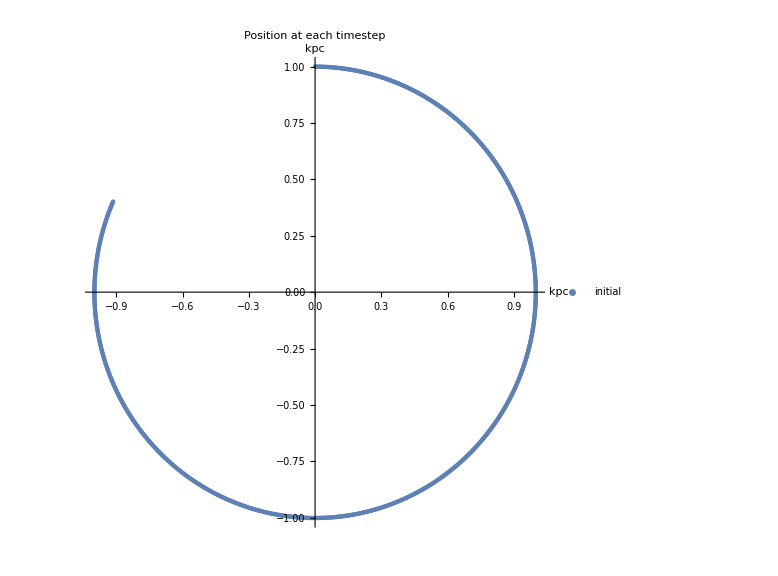

```mathematica
ch8posgraph = ListPlot[{ch8pos},AspectRatio->1,ImageSize->Large,PlotLegends->{"initial","after 1 timestep","after 2 timesteps"},AxesLabel->{"kpc","kpc"}, PlotLabel->"Position at each timestep"]
```

#### Velocity Dispersion

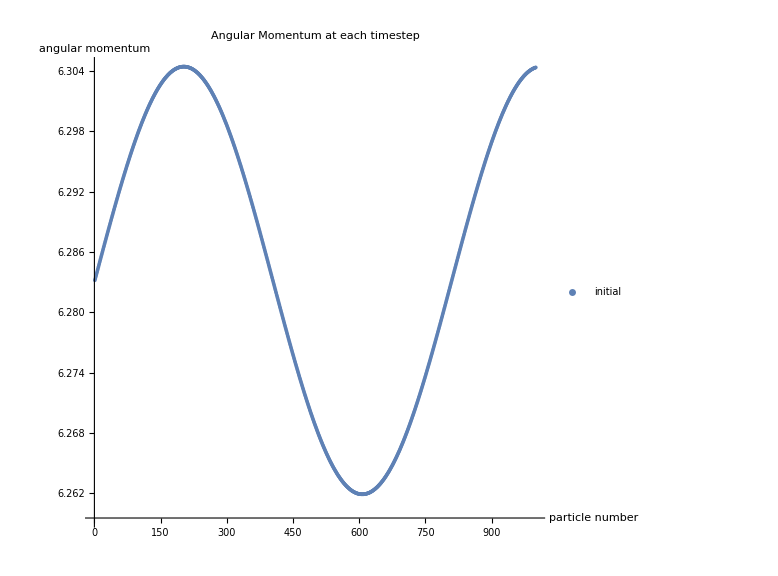

```mathematica
ch8AM = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/AM8.csv",{"Data",1;;1000,1}];
ch8AMgraph = ListPlot[{ch8AM},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"initial","after 1 timestep","after 2 timesteps"},AxesLabel->{"particle number","angular momentum"}, PlotLabel-> "Angular Momentum at each timestep"]
```

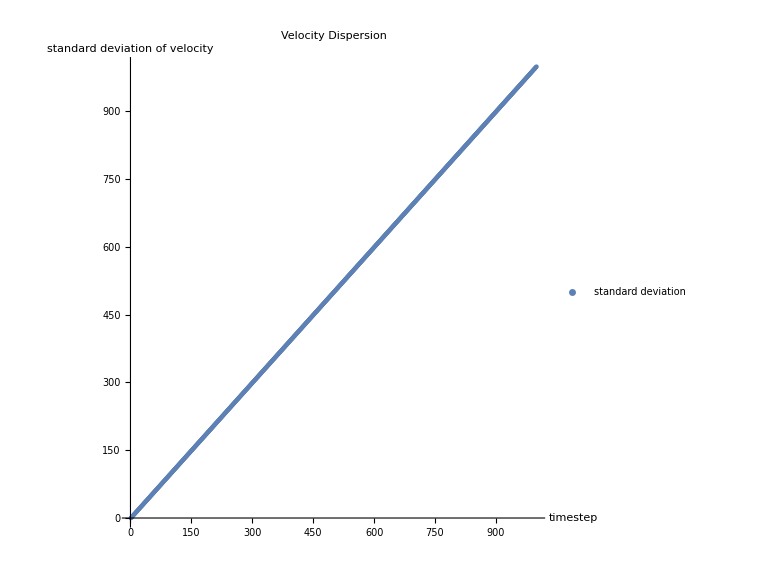

```mathematica
ch8SD = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/SD8.csv",{"Data",1;;1000,1}];
ch8SDgraph = ListPlot[{ch8SD},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"standard deviation"},AxesLabel->{"timestep","standard deviation of velocity"}, PlotLabel-> "Velocity Dispersion"]
```

### Version 10: pointmass potential dimensionless units throughout dot products, position, and velocity. Euler integrator with velocity updated before position. 1 test particle r0 = 15 kpc 20 timesteps of 100000 years each (decreased timestep by /10; was originally half of orbital period) mass of the galaxy estimated at 1,000,000,000 times mass of the sun

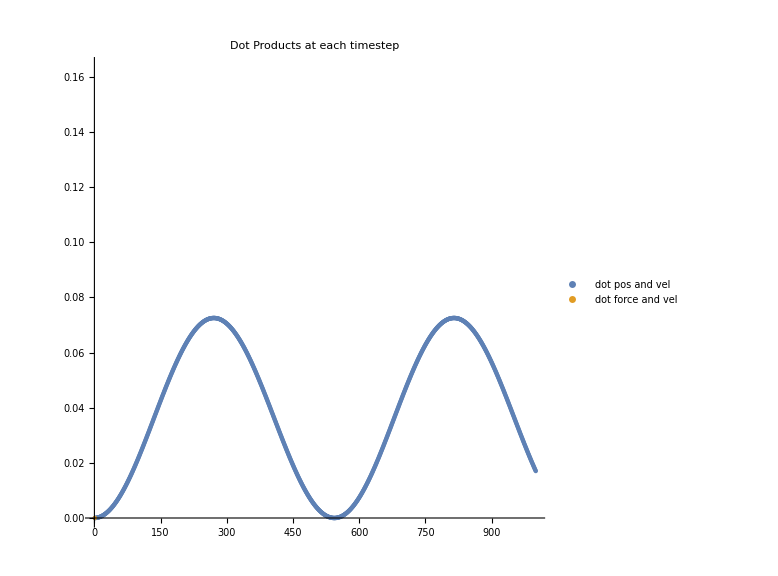

```mathematica
ch10dotposvel = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test10.csv",{"Data",1;;1000,1}];
ch10dotforcevel = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test10.csv",{"Data",1;;100,2}];
ch10magforce = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test10.csv",{"Data",1;;20,3}];
ch10magvel = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test10.csv",{"Data",1;;20,4}];
ch10magpos = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test10.csv",{"Data",1;;20,5}];
ch10pos = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test10.csv",{"Data",1;;1000,6;;7}];
ch10vel = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test10.csv",{"Data",1;;20,9;;10}];
ch10dotgraph = ListPlot[{ch10dotposvel,ch10dotforcevel},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"dot pos and vel","dot force and vel"}
, PlotLabel->"Dot Products at each timestep"]
```

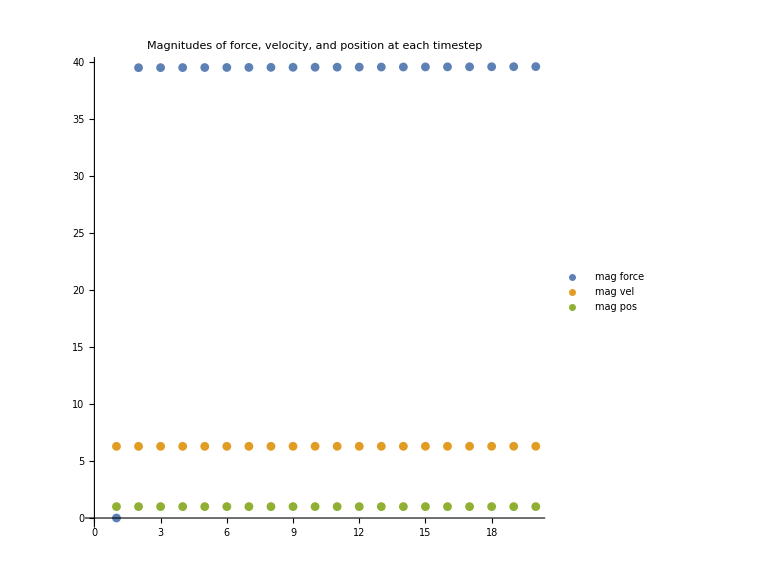

```mathematica
ch10maggraph = ListPlot[{ch10magforce,ch10magvel,ch10magpos},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"mag force","mag vel","mag pos"}, PlotLabel->"Magnitudes of force, velocity, and position at each timestep"]
```

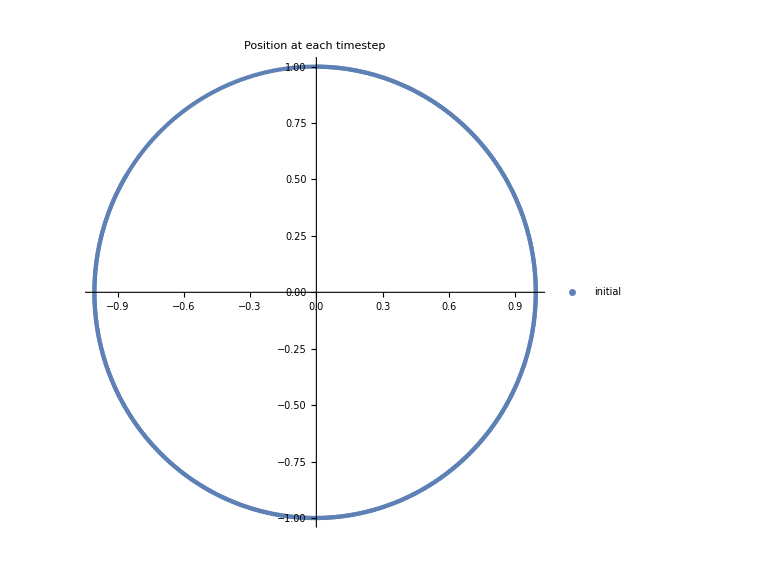

```mathematica
ch10posgraph = ListPlot[{ch10pos},AspectRatio->1,PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"initial","after 1 timestep","after 2 timesteps"}, PlotLabel->"Position at each timestep"]
```

## Differences

### Version 6 vs version 8 (doing calculations in dimensionless units vs not)

```mathematica
ch6pos
ch8pos
```

{{28.3415,4.62852×10^17},{2.05384×10^16,4.62852×10^17},{4.10747×10^16,4.62803×10^17},{6.16067×10^16,4.62707×10^17},{8.21324×10^16,4.62563×10^17},{1.0265×10^17,4.62373×10^17},{1.23157×10^17,4.62135×10^17},{1.43651×10^17,4.61851×10^17},{1.64132×10^17,4.61523×10^17},{1.84597×10^17,4.61149×10^17},{2.05044×10^17,4.60733×10^17},{2.25473×10^17,4.60273×10^17}}

{{6.12323×10^-17,1.},{0.00512924,0.999974},{0.0102584,0.999921},{0.0153872,0.999842},{0.0205156,0.999737},{0.0256435,0.999605},{0.0307707,0.999448},{0.0358971,0.999263},{0.0410226,0.999053},{0.046147,0.998816},{0.0512702,0.998553},{0.056392,0.998264},{0.0615123,0.997948},{0.066631,0.997607},{0.071748,0.997239},{0.0768631,0.996844},{0.0819761,0.996424},{0.087087,0.995977},{0.0921957,0.995504},{0.0973018,0.995005},{0.102405,0.994479},{0.107506,0.993928},{0.112604,0.99335},{0.1177,0.992746},{0.122792,0.992116},{0.12788,0.99146},{0.132966,0.990778},{0.138048,0.99007},{0.143126,0.989335},{0.148201,0.988575},{0.153271,0.987788},{0.158338,0.986976},{0.1634,0.986138},{0.168458,0.985273},{0.173512,0.984383},{0.178561,0.983467},{0.183606,0.982525},{0.188645,0.981557},{0.19368,0.980563},{0.198709,0.979543},{0.203734,0.978498},{0.208753,0.977426},{0.213766,0.976329},{0.218774,0.975207},{0.223776,0.974058},{0.228772,0.972884},{0.233762,0.971685},{0.238746,0.97046},{0.243724,0.969209},{0.248695,0.967933},{0.25366,0.966631},{0.258618,0.965304},{0.263569,0.963951},{0.268513,0.962573},{0.27345,0.961169},{0.27838,0.959741},{0.283303,0.958287},{0.288218,0.956807},{0.293126,0.955303},{0.298026,0.953773},{0.302918,0.952219},{0.307802,0.950639},{0.312678,0.949034},{0.317545,0.947404},{0.322405,0.945749},{0.327256,0.944069},{0.332098,0.942365},{0.336931,0.940635},{0.341756,0.938881},{0.346571,0.937102},{0.351378,0.935298},{0.356175,0.93347},{0.360963,0.931617},{0.365741,0.92974},{0.37051,0.927838},{0.375269,0.925911},{0.380018,0.923961},{0.384757,0.921985},{0.389486,0.919986},{0.394204,0.917962},{0.398912,0.915914},{0.40361,0.913842},{0.408297,0.911746},{0.412974,0.909626},{0.417639,0.907482},{0.422293,0.905314},{0.426937,0.903122},{0.431569,0.900907},{0.436189,0.898667},{0.440798,0.896404},{0.445396,0.894117},{0.449982,0.891807},{0.454556,0.889473},{0.459118,0.887116},{0.463668,0.884735},{0.468205,0.882331},{0.472731,0.879904},{0.477243,0.877454},{0.481744,0.87498},{0.486231,0.872483},{0.490706,0.869964},{0.495168,0.867421},{0.499616,0.864856},{0.504052,0.862268},{0.508474,0.859657},{0.512883,0.857023},{0.517278,0.854367},{0.52166,0.851688},{0.526028,0.848987},{0.530382,0.846263},{0.534722,0.843518},{0.539048,0.840749},{0.54336,0.837959},{0.547658,0.835147},{0.551941,0.832312},{0.556209,0.829456},{0.560463,0.826578},{0.564702,0.823678},{0.568926,0.820756},{0.573135,0.817813},{0.577329,0.814848},{0.581508,0.811861},{0.585672,0.808853},{0.58982,0.805824},{0.593952,0.802774},{0.598069,0.799702},{0.60217,0.796609},{0.606255,0.793496},{0.610324,0.790361},{0.614377,0.787206},{0.618414,0.784029},{0.622435,0.780833},{0.626439,0.777615},{0.630426,0.774377},{0.634397,0.771119},{0.638352,0.76784},{0.642289,0.764541},{0.64621,0.761222},{0.650113,0.757882},{0.653999,0.754523},{0.657868,0.751144},{0.66172,0.747745},{0.665554,0.744326},{0.669371,0.740888},{0.67317,0.73743},{0.676951,0.733953},{0.680715,0.730456},{0.68446,0.72694},{0.688187,0.723405},{0.691897,0.719851},{0.695588,0.716278},{0.69926,0.712686},{0.702915,0.709075},{0.70655,0.705445},{0.710167,0.701797},{0.713765,0.69813},{0.717345,0.694445},{0.720905,0.690742},{0.724447,0.68702},{0.727969,0.68328},{0.731473,0.679522},{0.734956,0.675746},{0.738421,0.671953},{0.741866,0.668142},{0.745291,0.664313},{0.748697,0.660466},{0.752083,0.656602},{0.755449,0.652721},{0.758796,0.648823},{0.762122,0.644907},{0.765428,0.640975},{0.768714,0.637025},{0.77198,0.633059},{0.775225,0.629076},{0.77845,0.625076},{0.781654,0.62106},{0.784838,0.617028},{0.788001,0.612979},{0.791143,0.608914},{0.794264,0.604833},{0.797365,0.600736},{0.800444,0.596623},{0.803502,0.592495},{0.806539,0.588351},{0.809555,0.584191},{0.812549,0.580016},{0.815522,0.575826},{0.818474,0.57162},{0.821404,0.567399},{0.824312,0.563164},{0.827198,0.558913},{0.830063,0.554648},{0.832905,0.550368},{0.835726,0.546074},{0.838525,0.541765},{0.841301,0.537442},{0.844055,0.533105},{0.846788,0.528753},{0.849497,0.524388},{0.852185,0.520009},{0.854849,0.515616},{0.857492,0.51121},{0.860111,0.50679},{0.862708,0.502356},{0.865282,0.49791},{0.867834,0.49345},{0.870362,0.488977},{0.872868,0.484492},{0.87535,0.479993},{0.877809,0.475482},{0.880246,0.470959},{0.882659,0.466422},{0.885048,0.461874},{0.887415,0.457314},{0.889757,0.452741},{0.892077,0.448156},{0.894373,0.44356},{0.896645,0.438952},{0.898894,0.434332},{0.901119,0.429701},{0.90332,0.425059},{0.905497,0.420405},{0.907651,0.41574},{0.90978,0.411065},{0.911885,0.406378},{0.913967,0.401681},{0.916024,0.396973},{0.918057,0.392254},{0.920066,0.387526},{0.922051,0.382787},{0.924011,0.378038},{0.925947,0.373279},{0.927859,0.36851},{0.929746,0.363731},{0.931608,0.358943},{0.933446,0.354145},{0.935259,0.349338},{0.937048,0.344522},{0.938812,0.339697},{0.940551,0.334863},{0.942265,0.330019},{0.943955,0.325168},{0.945619,0.320307},{0.947259,0.315438},{0.948873,0.310561},{0.950463,0.305676},{0.952028,0.300782},{0.953567,0.295881},{0.955081,0.290972},{0.95657,0.286055},{0.958034,0.281131},{0.959473,0.276199},{0.960886,0.27126},{0.962274,0.266314},{0.963636,0.26136},{0.964973,0.2564},{0.966285,0.251433},{0.967571,0.24646},{0.968832,0.24148},{0.970067,0.236493},{0.971276,0.231501},{0.97246,0.226502},{0.973618,0.221497},{0.974751,0.216487},{0.975857,0.21147},{0.976939,0.206448},{0.977994,0.201421},{0.979023,0.196388},{0.980027,0.191351},{0.981005,0.186308},{0.981957,0.18126},{0.982883,0.176207},{0.983783,0.17115},{0.984657,0.166088},{0.985505,0.161022},{0.986328,0.155952},{0.987124,0.150878},{0.987894,0.145799},{0.988638,0.140717},{0.989356,0.135631},{0.990048,0.130541},{0.990714,0.125448},{0.991354,0.120352},{0.991967,0.115253},{0.992555,0.11015},{0.993116,0.105045},{0.993651,0.0999364},{0.99416,0.0948255},{0.994643,0.0897122},{0.995099,0.0845965},{0.995529,0.0794786},{0.995933,0.0743585},{0.996311,0.0692366},{0.996662,0.0641127},{0.996987,0.0589872},{0.997286,0.0538602},{0.997559,0.0487317},{0.997805,0.0436019},{0.998025,0.038471},{0.998219,0.0333391},{0.998386,0.0282063},{0.998527,0.0230727},{0.998642,0.0179385},{0.99873,0.0128039},{0.998792,0.00766894},{0.998828,0.00253377},{0.998837,-0.00260147},{0.99882,-0.00773664},{0.998777,-0.0128716},{0.998707,-0.0180062},{0.998611,-0.0231404},{0.998489,-0.0282739},{0.99834,-0.0334067},{0.998165,-0.0385387},{0.997964,-0.0436696},{0.997736,-0.0487993},{0.997483,-0.0539278},{0.997202,-0.0590548},{0.996896,-0.0641803},{0.996563,-0.0693041},{0.996204,-0.0744261},{0.995819,-0.0795461},{0.995408,-0.084664},{0.99497,-0.0897797},{0.994506,-0.094893},{0.994016,-0.100004},{0.9935,-0.105112},{0.992957,-0.110217},{0.992389,-0.11532},{0.991794,-0.120419},{0.991173,-0.125516},{0.990526,-0.130609},{0.989853,-0.135698},{0.989153,-0.140784},{0.988428,-0.145866},{0.987677,-0.150945},{0.986899,-0.156019},{0.986096,-0.16109},{0.985267,-0.166156},{0.984411,-0.171217},{0.98353,-0.176275},{0.982623,-0.181327},{0.98169,-0.186375},{0.980731,-0.191418},{0.979746,-0.196456},{0.978736,-0.201488},{0.977699,-0.206516},{0.976637,-0.211537},{0.97555,-0.216554},{0.974436,-0.221564},{0.973297,-0.226569},{0.972132,-0.231568},{0.970942,-0.236561},{0.969726,-0.241547},{0.968484,-0.246527},{0.967217,-0.251501},{0.965925,-0.256468},{0.964607,-0.261428},{0.963263,-0.266382},{0.961895,-0.271328},{0.960501,-0.276267},{0.959081,-0.281199},{0.957637,-0.286124},{0.956167,-0.291041},{0.954672,-0.29595},{0.953152,-0.300852},{0.951606,-0.305745},{0.950036,-0.310631},{0.948441,-0.315508},{0.946821,-0.320377},{0.945175,-0.325238},{0.943505,-0.33009},{0.94181,-0.334933},{0.940091,-0.339768},{0.938346,-0.344593},{0.936577,-0.34941},{0.934783,-0.354217},{0.932965,-0.359015},{0.931122,-0.363804},{0.929254,-0.368583},{0.927362,-0.373352},{0.925446,-0.378112},{0.923505,-0.382861},{0.92154,-0.387601},{0.919551,-0.39233},{0.917537,-0.397049},{0.9155,-0.401757},{0.913438,-0.406455},{0.911352,-0.411142},{0.909242,-0.415819},{0.907109,-0.420484},{0.904951,-0.425139},{0.90277,-0.429782},{0.900564,-0.434414},{0.898336,-0.439034},{0.896083,-0.443643},{0.893807,-0.44824},{0.891507,-0.452826},{0.889184,-0.457399},{0.886838,-0.461961},{0.884468,-0.46651},{0.882075,-0.471047},{0.879659,-0.475572},{0.877219,-0.480084},{0.874757,-0.484583},{0.872271,-0.48907},{0.869763,-0.493544},{0.867232,-0.498005},{0.864678,-0.502453},{0.862101,-0.506887},{0.859501,-0.511308},{0.856879,-0.515716},{0.854234,-0.52011},{0.851567,-0.524491},{0.848877,-0.528858},{0.846166,-0.533211},{0.843431,-0.537549},{0.840675,-0.541874},{0.837897,-0.546184},{0.835096,-0.550481},{0.832274,-0.554762},{0.829429,-0.559029},{0.826563,-0.563281},{0.823675,-0.567519},{0.820766,-0.571741},{0.817835,-0.575949},{0.814882,-0.580141},{0.811908,-0.584318},{0.808912,-0.58848},{0.805896,-0.592626},{0.802858,-0.596757},{0.799799,-0.600872},{0.796719,-0.604971},{0.793618,-0.609055},{0.790496,-0.613122},{0.787353,-0.617173},{0.78419,-0.621208},{0.781006,-0.625227},{0.777802,-0.629229},{0.774577,-0.633215},{0.771331,-0.637184},{0.768066,-0.641136},{0.76478,-0.645071},{0.761474,-0.64899},{0.758148,-0.652891},{0.754803,-0.656775},{0.751437,-0.660642},{0.748052,-0.664492},{0.744647,-0.668324},{0.741222,-0.672138},{0.737778,-0.675935},{0.734314,-0.679714},{0.730832,-0.683476},{0.72733,-0.687219},{0.723809,-0.690944},{0.720268,-0.694651},{0.716709,-0.69834},{0.713131,-0.70201},{0.709535,-0.705663},{0.70592,-0.709296},{0.702286,-0.712911},{0.698633,-0.716507},{0.694963,-0.720084},{0.691274,-0.723643},{0.687567,-0.727182},{0.683842,-0.730702},{0.680099,-0.734203},{0.676338,-0.737685},{0.672559,-0.741147},{0.668763,-0.74459},{0.664949,-0.748014},{0.661117,-0.751417},{0.657268,-0.754801},{0.653402,-0.758165},{0.649519,-0.761509},{0.645619,-0.764834},{0.641701,-0.768138},{0.637767,-0.771422},{0.633816,-0.774685},{0.629849,-0.777929},{0.625865,-0.781152},{0.621864,-0.784354},{0.617847,-0.787536},{0.613814,-0.790697},{0.609765,-0.793837},{0.6057,-0.796956},{0.601619,-0.800055},{0.597522,-0.803132},{0.593409,-0.806189},{0.589281,-0.809224},{0.585138,-0.812238},{0.580978,-0.815231},{0.576804,-0.818202},{0.572615,-0.821152},{0.56841,-0.82408},{0.564191,-0.826987},{0.559957,-0.829871},{0.555708,-0.832734},{0.551444,-0.835576},{0.547166,-0.838395},{0.542874,-0.841192},{0.538567,-0.843967},{0.534247,-0.84672},{0.529912,-0.849451},{0.525563,-0.852159},{0.521201,-0.854846},{0.516824,-0.857509},{0.512435,-0.86015},{0.508031,-0.862769},{0.503615,-0.865365},{0.499185,-0.867938},{0.494742,-0.870488},{0.490286,-0.873016},{0.485818,-0.87552},{0.481336,-0.878002},{0.476842,-0.880461},{0.472335,-0.882896},{0.467816,-0.885308},{0.463285,-0.887697},{0.458742,-0.890063},{0.454186,-0.892406},{0.449619,-0.894724},{0.445039,-0.89702},{0.440448,-0.899292},{0.435846,-0.90154},{0.431232,-0.903765},{0.426607,-0.905966},{0.42197,-0.908143},{0.417323,-0.910296},{0.412664,-0.912426},{0.407995,-0.914531},{0.403315,-0.916613},{0.398625,-0.91867},{0.393923,-0.920703},{0.389212,-0.922712},{0.38449,-0.924697},{0.379759,-0.926658},{0.375017,-0.928594},{0.370266,-0.930506},{0.365504,-0.932394},{0.360734,-0.934257},{0.355953,-0.936096},{0.351164,-0.93791},{0.346365,-0.939699},{0.341557,-0.941464},{0.33674,-0.943204},{0.331914,-0.944919},{0.32708,-0.946609},{0.322237,-0.948275},{0.317385,-0.949916},{0.312526,-0.951532},{0.307658,-0.953123},{0.302781,-0.954688},{0.297897,-0.956229},{0.293006,-0.957745},{0.288106,-0.959235},{0.283199,-0.960701},{0.278284,-0.962141},{0.273363,-0.963556},{0.268434,-0.964946},{0.263498,-0.96631},{0.258555,-0.967649},{0.253605,-0.968963},{0.248649,-0.970251},{0.243686,-0.971514},{0.238716,-0.972751},{0.233741,-0.973963},{0.228759,-0.975149},{0.223771,-0.976309},{0.218778,-0.977444},{0.213779,-0.978554},{0.208774,-0.979637},{0.203763,-0.980695},{0.198747,-0.981727},{0.193726,-0.982734},{0.1887,-0.983715},{0.183669,-0.984669},{0.178634,-0.985598},{0.173593,-0.986502},{0.168548,-0.987379},{0.163499,-0.98823},{0.158445,-0.989056},{0.153387,-0.989855},{0.148325,-0.990629},{0.143259,-0.991376},{0.13819,-0.992098},{0.133116,-0.992794},{0.12804,-0.993463},{0.12296,-0.994106},{0.117876,-0.994724},{0.11279,-0.995315},{0.107701,-0.99588},{0.102608,-0.996419},{0.0975135,-0.996932},{0.0924161,-0.997419},{0.0873163,-0.997879},{0.0822141,-0.998314},{0.0771098,-0.998722},{0.0720035,-0.999104},{0.0668953,-0.99946},{0.0617854,-0.999789},{0.0566738,-1.00009},{0.0515607,-1.00037},{0.0464463,-1.00062},{0.0413307,-1.00085},{0.0362139,-1.00104},{0.0310963,-1.00122},{0.0259778,-1.00136},{0.0208586,-1.00148},{0.0157389,-1.00157},{0.0106188,-1.00164},{0.00549835,-1.00168},{0.000377799,-1.0017},{-0.00474276,-1.00168},{-0.0098632,-1.00165},{-0.0149834,-1.00158},{-0.0201032,-1.00149},{-0.0252224,-1.00137},{-0.030341,-1.00123},{-0.0354588,-1.00106},{-0.0405757,-1.00087},{-0.0456915,-1.00064},{-0.0508061,-1.0004},{-0.0559194,-1.00012},{-0.0610312,-0.999821},{-0.0661414,-0.999494},{-0.0712499,-0.999141},{-0.0763565,-0.998761},{-0.0814611,-0.998356},{-0.0865635,-0.997924},{-0.0916637,-0.997466},{-0.0967615,-0.996982},{-0.101857,-0.996472},{-0.106949,-0.995935},{-0.112039,-0.995373},{-0.117126,-0.994784},{-0.12221,-0.994169},{-0.12729,-0.993529},{-0.132367,-0.992862},{-0.137441,-0.992169},{-0.142511,-0.99145},{-0.147578,-0.990705},{-0.15264,-0.989934},{-0.157699,-0.989137},{-0.162753,-0.988314},{-0.167803,-0.987465},{-0.172849,-0.98659},{-0.17789,-0.98569},{-0.182927,-0.984763},{-0.187958,-0.983811},{-0.192985,-0.982833},{-0.198007,-0.981829},{-0.203023,-0.980799},{-0.208035,-0.979744},{-0.21304,-0.978663},{-0.21804,-0.977556},{-0.223035,-0.976423},{-0.228023,-0.975265},{-0.233006,-0.974082},{-0.237982,-0.972872},{-0.242953,-0.971638},{-0.247917,-0.970377},{-0.252874,-0.969092},{-0.257825,-0.967781},{-0.262769,-0.966444},{-0.267706,-0.965082},{-0.272636,-0.963695},{-0.277558,-0.962283},{-0.282474,-0.960845},{-0.287382,-0.959382},{-0.292283,-0.957894},{-0.297176,-0.95638},{-0.302061,-0.954842},{-0.306938,-0.953279},{-0.311807,-0.95169},{-0.316668,-0.950077},{-0.321521,-0.948438},{-0.326365,-0.946775},{-0.331201,-0.945087},{-0.336028,-0.943374},{-0.340846,-0.941636},{-0.345655,-0.939874},{-0.350456,-0.938087},{-0.355247,-0.936275},{-0.360028,-0.934439},{-0.3648,-0.932578},{-0.369563,-0.930693},{-0.374316,-0.928783},{-0.379059,-0.926849},{-0.383792,-0.924891},{-0.388515,-0.922908},{-0.393228,-0.920901},{-0.397931,-0.91887},{-0.402623,-0.916815},{-0.407304,-0.914736},{-0.411975,-0.912633},{-0.416635,-0.910506},{-0.421284,-0.908354},{-0.425922,-0.906179},{-0.430549,-0.903981},{-0.435165,-0.901758},{-0.439769,-0.899512},{-0.444361,-0.897242},{-0.448942,-0.894949},{-0.453511,-0.892632},{-0.458068,-0.890292},{-0.462614,-0.887928},{-0.467147,-0.885541},{-0.471667,-0.883131},{-0.476176,-0.880698},{-0.480672,-0.878241},{-0.485155,-0.875762},{-0.489626,-0.873259},{-0.494083,-0.870734},{-0.498528,-0.868186},{-0.50296,-0.865614},{-0.507378,-0.86302},{-0.511783,-0.860404},{-0.516175,-0.857765},{-0.520553,-0.855103},{-0.524917,-0.852419},{-0.529268,-0.849713},{-0.533605,-0.846984},{-0.537927,-0.844233},{-0.542236,-0.84146},{-0.54653,-0.838664},{-0.55081,-0.835847},{-0.555076,-0.833008},{-0.559327,-0.830146},{-0.563563,-0.827263},{-0.567784,-0.824359},{-0.571991,-0.821432},{-0.576182,-0.818484},{-0.580359,-0.815515},{-0.58452,-0.812524},{-0.588666,-0.809512},{-0.592796,-0.806479},{-0.596911,-0.803424},{-0.60101,-0.800348},{-0.605093,-0.797251},{-0.609161,-0.794134},{-0.613212,-0.790995},{-0.617247,-0.787836},{-0.621266,-0.784656},{-0.625269,-0.781455},{-0.629255,-0.778234},{-0.633225,-0.774992},{-0.637178,-0.77173},{-0.641115,-0.768448},{-0.645034,-0.765145},{-0.648937,-0.761823},{-0.652822,-0.75848},{-0.656691,-0.755118},{-0.660542,-0.751735},{-0.664376,-0.748333},{-0.668192,-0.744911},{-0.671991,-0.74147},{-0.675772,-0.738009},{-0.679535,-0.734529},{-0.683281,-0.731029},{-0.687008,-0.727511},{-0.690718,-0.723973},{-0.694409,-0.720416},{-0.698082,-0.71684},{-0.701737,-0.713245},{-0.705373,-0.709632},{-0.708991,-0.706},{-0.71259,-0.702349},{-0.716171,-0.69868},{-0.719732,-0.694993},{-0.723275,-0.691287},{-0.726798,-0.687563},{-0.730303,-0.683821},{-0.733788,-0.680061},{-0.737254,-0.676283},{-0.740701,-0.672488},{-0.744128,-0.668674},{-0.747536,-0.664843},{-0.750924,-0.660995},{-0.754292,-0.657129},{-0.75764,-0.653246},{-0.760969,-0.649346},{-0.764277,-0.645429},{-0.767566,-0.641495},{-0.770834,-0.637544},{-0.774082,-0.633576},{-0.777309,-0.629591},{-0.780516,-0.62559},{-0.783703,-0.621573},{-0.786869,-0.617539},{-0.790014,-0.613489},{-0.793139,-0.609422},{-0.796242,-0.60534},{-0.799325,-0.601242},{-0.802387,-0.597128},{-0.805428,-0.592998},{-0.808447,-0.588853},{-0.811445,-0.584692},{-0.814422,-0.580516},{-0.817377,-0.576325},{-0.820311,-0.572118},{-0.823223,-0.567896},{-0.826114,-0.56366},{-0.828983,-0.559408},{-0.83183,-0.555142},{-0.834655,-0.550861},{-0.837459,-0.546566},{-0.84024,-0.542257},{-0.842999,-0.537933},{-0.845736,-0.533595},{-0.848451,-0.529243},{-0.851143,-0.524877},{-0.853813,-0.520497},{-0.856461,-0.516103},{-0.859086,-0.511696},{-0.861688,-0.507276},{-0.864268,-0.502842},{-0.866825,-0.498395},{-0.869359,-0.493935},{-0.87187,-0.489461},{-0.874358,-0.484975},{-0.876824,-0.480476},{-0.879266,-0.475965},{-0.881685,-0.471441},{-0.884081,-0.466904},{-0.886454,-0.462356},{-0.888803,-0.457795},{-0.891129,-0.453222},{-0.893431,-0.448637},{-0.89571,-0.44404},{-0.897966,-0.439432},{-0.900197,-0.434812},{-0.902405,-0.430181},{-0.90459,-0.425538},{-0.90675,-0.420884},{-0.908887,-0.416219},{-0.911,-0.411543},{-0.913088,-0.406856},{-0.915153,-0.402159},{-0.917193,-0.397451},{-0.91921,-0.392732},{-0.921202,-0.388003},{-0.92317,-0.383264},{-0.925114,-0.378515},{-0.927033,-0.373756},{-0.928928,-0.368987},{-0.930798,-0.364208},{-0.932644,-0.35942},{-0.934466,-0.354622},{-0.936263,-0.349815},{-0.938035,-0.344999},{-0.939782,-0.340173},{-0.941505,-0.335339},{-0.943203,-0.330496},{-0.944876,-0.325644},{-0.946524,-0.320783},{-0.948147,-0.315915},{-0.949745,-0.311037},{-0.951318,-0.306152},{-0.952867,-0.301258},{-0.95439,-0.296357},{-0.955888,-0.291448},{-0.95736,-0.286531},{-0.958808,-0.281606},{-0.96023,-0.276675},{-0.961627,-0.271735},{-0.962999,-0.266789},{-0.964345,-0.261836},{-0.965666,-0.256875},{-0.966962,-0.251908},{-0.968232,-0.246935},{-0.969476,-0.241955},{-0.970695,-0.236968},{-0.971888,-0.231975},{-0.973056,-0.226976},{-0.974198,-0.221972},{-0.975315,-0.216961},{-0.976406,-0.211945},{-0.977471,-0.206923},{-0.97851,-0.201895},{-0.979523,-0.196862},{-0.980511,-0.191824},{-0.981473,-0.186781},{-0.982409,-0.181733},{-0.983319,-0.176681},{-0.984203,-0.171623},{-0.985062,-0.166561},{-0.985894,-0.161495},{-0.9867,-0.156424},{-0.98748,-0.15135},{-0.988235,-0.146271},{-0.988963,-0.141189},{-0.989665,-0.136102},{-0.990341,-0.131013},{-0.990991,-0.125919},{-0.991615,-0.120823},{-0.992213,-0.115723},{-0.992785,-0.11062},{-0.99333,-0.105514},{-0.993849,-0.100406},{-0.994342,-0.0952946},{-0.994809,-0.0901809},{-0.99525,-0.0850649},{-0.995664,-0.0799466},{-0.996052,-0.0748261},{-0.996414,-0.0697038},{-0.99675,-0.0645795},{-0.997059,-0.0594536},{-0.997342,-0.0543261},{-0.997599,-0.0491972},{-0.997829,-0.044067},{-0.998034,-0.0389356},{-0.998211,-0.0338032},{-0.998363,-0.0286699},{-0.998488,-0.0235358},{-0.998587,-0.0184011},{-0.99866,-0.013266},{-0.998706,-0.00813045},{-0.998726,-0.00299473},{-0.998719,0.00214108},{-0.998687,0.00727683},{-0.998628,0.0124124},{-0.998542,0.0175476},{-0.99843,0.0226824},{-0.998292,0.0278166},{-0.998128,0.03295},{-0.997937,0.0380826},{-0.99772,0.0432141},{-0.997477,0.0483446},{-0.997207,0.0534737},{-0.996911,0.0586014},{-0.996589,0.0637276},{-0.99624,0.0688521},{-0.995866,0.0739748},{-0.995465,0.0790956},{-0.995037,0.0842143},{-0.994584,0.0893307},{-0.994104,0.0944448},{-0.993598,0.0995564},{-0.993066,0.104665},{-0.992507,0.109772},{-0.991923,0.114875},{-0.991312,0.119975},{-0.990675,0.125072},{-0.990012,0.130166},{-0.989323,0.135256},{-0.988608,0.140343},{-0.987866,0.145426},{-0.987099,0.150506},{-0.986306,0.155581},{-0.985486,0.160652},{-0.984641,0.165719},{-0.98377,0.170782},{-0.982872,0.17584},{-0.981949,0.180893},{-0.981,0.185942},{-0.980025,0.190986},{-0.979024,0.196025},{-0.977997,0.201058},{-0.976945,0.206086},{-0.975867,0.211109},{-0.974763,0.216126},{-0.973633,0.221138},{-0.972478,0.226144},{-0.971296,0.231144},{-0.97009,0.236137},{-0.968858,0.241125},{-0.9676,0.246106},{-0.966316,0.25108},{-0.965008,0.256048},{-0.963673,0.261009},{-0.962313,0.265964},{-0.960928,0.270911},{-0.959518,0.275851},{-0.958082,0.280784},{-0.956621,0.28571},{-0.955135,0.290627},{-0.953623,0.295538},{-0.952087,0.30044},{-0.950525,0.305335},{-0.948938,0.310221},{-0.947326,0.3151},{-0.945689,0.31997},{-0.944027,0.324831},{-0.942341,0.329684},{-0.940629,0.334528},{-0.938893,0.339364},{-0.937132,0.34419},{-0.935346,0.349008},{-0.933535,0.353816},{-0.9317,0.358615},{-0.92984,0.363404},{-0.927956,0.368184},{-0.926047,0.372954},{-0.924114,0.377714},{-0.922156,0.382465},{-0.920174,0.387205},{-0.918168,0.391935},{-0.916137,0.396655},{-0.914083,0.401364}}

### Sun Earth vs og Sun Earth

```mathematica
Differences[{SEpos,SEogpos}]
```

{{{0.,0.},{-1.×10^-6,2.9×10^-6},{-1.×10^-6,5.×10^-6},{-2.×10^-6,9.×10^-6},{-4.×10^-6,0.00001},{-5.×10^-6,0.000014},{-7.×10^-6,0.000016},{-0.00001,0.000018},{-0.000012,0.000019},{-0.000015,0.000022},{-0.000019,0.000022},{-0.000022,0.000023},{-0.000026,0.000024},{-0.00003,0.000025},{-0.000034,0.000024},{-0.000038,0.000024},{-0.000042,0.000023},{-0.000046,0.000022},{-0.00005,0.000019},{-0.000055,0.000017},{-0.000058,0.000015},{-0.000062,0.000011},{-0.000066,8.×10^-6},{-0.0000694,4.×10^-6},{-0.00007258,-1.×10^-6},{-0.0000754,-5.×10^-6},{-0.000078,-0.000011},{-0.000081,-0.000017},{-0.000081,-0.000022},{-0.000083,-0.000028},{-0.000084,-0.000035},{-0.000084,-0.000041},{-0.000083,-0.000048},{-0.000083,-0.000055},{-0.000082,-0.000062},{-0.00008,-0.000069},{-0.000077,-0.000076},{-0.000074,-0.000083},{-0.00007,-0.000089},{-0.000066,-0.000096},{-0.000061,-0.000103},{-0.000056,-0.000108},{-0.00005,-0.000114},{-0.000044,-0.00012},{-0.000037,-0.000125},{-0.00003,-0.00013},{-0.000023,-0.000134},{-0.000014,-0.0001371},{-0.00001,-0.00014024},{0.00001,-0.0001429},{0.000012,-0.000145},{0.000021,-0.000147},{0.00003,-0.000147},{0.000041,-0.000147},{0.000051,-0.000147},{0.00006,-0.000146},{0.00007,-0.000144},{0.00008,-0.000141},{0.00009,-0.000138},{0.000099,-0.000134},{0.000109,-0.00013},{0.000118,-0.000125},{0.000127,-0.000119},{0.000136,-0.000113},{0.000144,-0.000105},{0.000153,-0.000098},{0.00016,-0.00009},{0.000168,-0.000081},{0.000174,-0.000071},{0.000181,-0.000061},{0.000187,-0.00006},{0.000192,-0.00004},{0.000197,-0.00003},{0.0002006,-0.00002},{0.0002037,-0.00001},{0.0002062,0.00001},{0.000208,0.00002},{0.000209,0.00003},{0.000209,0.00004},{0.000209,0.000061},{0.000206,0.000074},{0.000204,0.000087},{0.000201,0.000101},{0.000197,0.000115},{0.000192,0.000129},{0.000186,0.000142},{0.000179,0.000155},{0.000171,0.000167},{0.000162,0.00018},{0.000153,0.000192},{0.000143,0.000204},{0.000132,0.000215},{0.000119,0.000225},{0.000106,0.000235},{0.000093,0.000245},{0.000078,0.000253},{0.000063,0.000261},{0.000048,0.000267},{0.00003,0.000273},{0.000014,0.0002773}}}

## Sun/Earth System

### Original Euler

in AU and years
timestep = 0.1 years, 100 timesteps

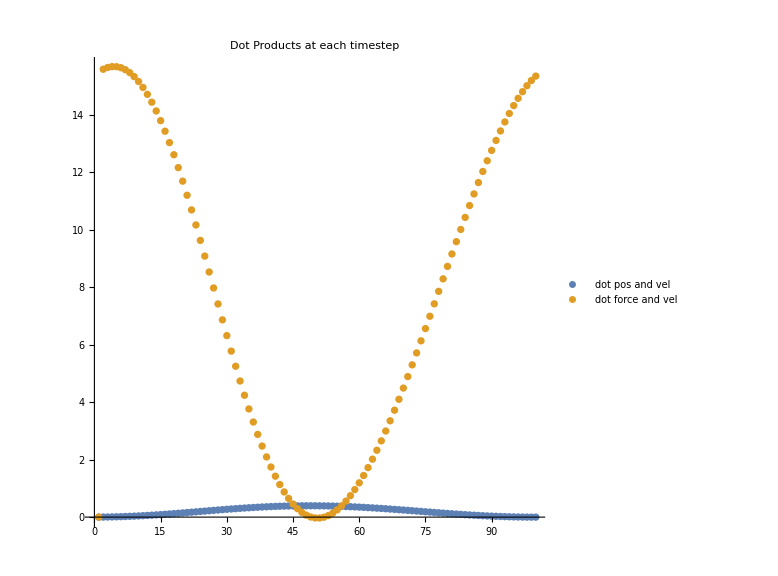

```mathematica
SEogdotposvel = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/SEog.csv",{"Data",1;;100,1}];
SEogdotforcevel = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/SEog.csv",{"Data",1;;100,2}];
SEogmagforce = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/SEog.csv",{"Data",1;;100,3}];
SEogmagvel = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/SEog.csv",{"Data",1;;100,4}];
SEogmagpos = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/SEog.csv",{"Data",1;;100,5}];
SEogpos = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/SEog.csv",{"Data",1;;100,6;;7}];
SEogvel = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/SEog.csv",{"Data",1;;100,9;;10}];
SEogdotgraph = ListPlot[{SEogdotposvel,SEogdotforcevel},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"dot pos and vel","dot force and vel"}, PlotLabel->"Dot Products at each timestep"]
```

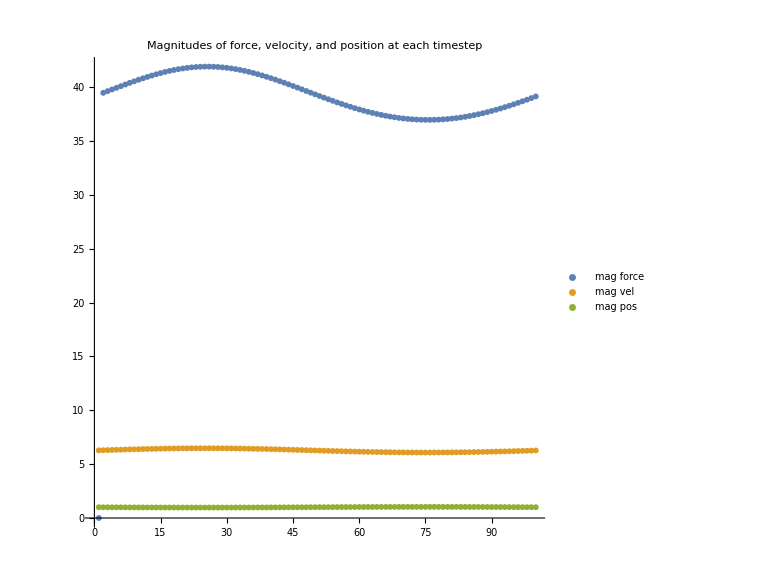

```mathematica
SEogmaggraph = ListPlot[{SEogmagforce,SEogmagvel,SEogmagpos},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"mag force","mag vel","mag pos"}, PlotLabel->"Magnitudes of force, velocity, and position at each timestep"]
```

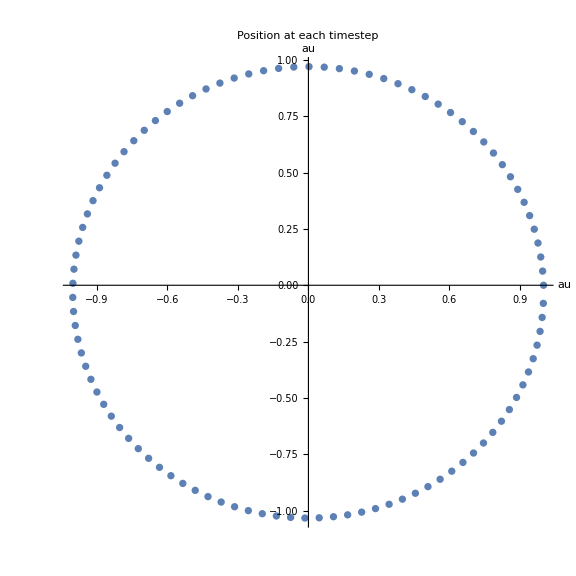

```mathematica
SEogposgraph = ListPlot[{SEogpos},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"initial","after 1 timestep","after 2 timesteps"},AxesLabel->{"au","au"}, PlotLabel->"Position at each timestep",ColorFunction->"TemperatureMap"]
```

### Current Euler

in AU and years
timestep = 0.1 years, 100 timesteps
switched order in which position and velocity are updated

```mathematica
SEdotposvel = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test9.csv",{"Data",1;;100,1}];
SEdotforcevel = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test9.csv",{"Data",1;;100,2}];
SEmagforce = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test9.csv",{"Data",1;;100,3}];
SEmagvel = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test9.csv",{"Data",1;;100,4}];
SEmagpos = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test9.csv",{"Data",1;;100,5}];
SEpos = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test9.csv",{"Data",1;;100,6;;7}];
SEvel = Import["/Users/clairerecamier/Desktop/Github/Streakline/power-spectra/test9.csv",{"Data",1;;100,9;;10}];
```

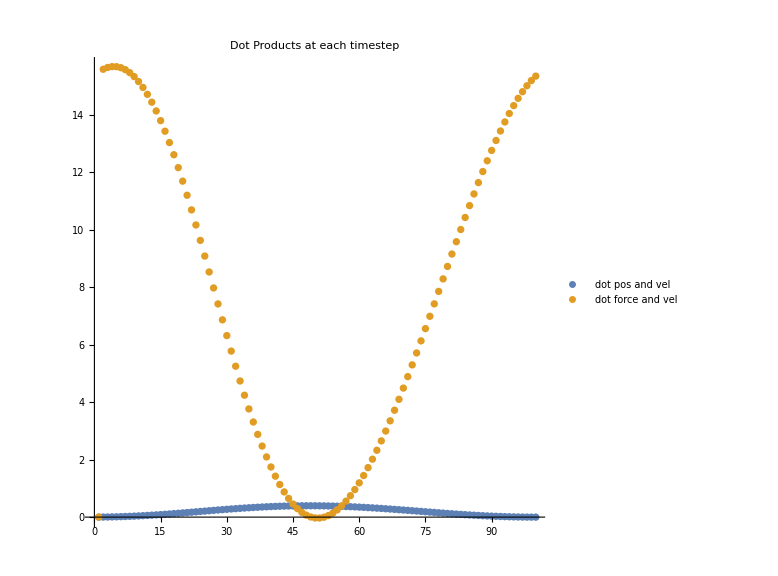

```mathematica
SEdotgraph = ListPlot[{SEdotposvel,SEdotforcevel},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"dot pos and vel","dot force and vel"}, PlotLabel->"Dot Products at each timestep"]
```

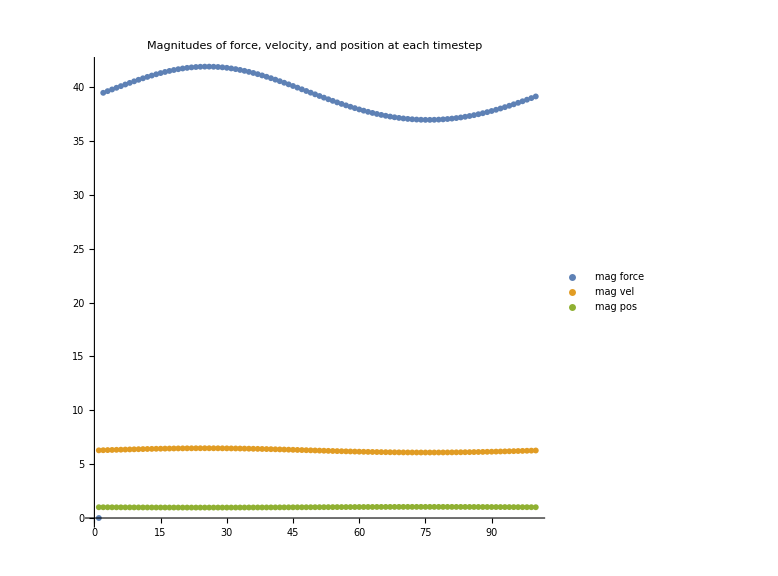

```mathematica
SEmaggraph = ListPlot[{SEmagforce,SEmagvel,SEmagpos},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"mag force","mag vel","mag pos"}, PlotLabel->"Magnitudes of force, velocity, and position at each timestep"]
```

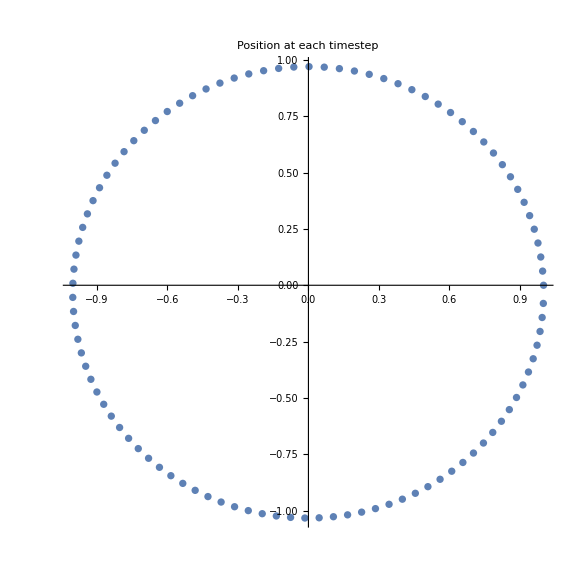

```mathematica
SEposgraph = ListPlot[{SEpos},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"initial","after 1 timestep","after 2 timesteps"}, PlotLabel->"Position at each timestep",ColorFunction->"TemperatureMap"]
```